Symbolic integration of the cosine-weighted constant visibility function ∫cosθ sinθⅆθ= -1/2 cos^2 θ
Integration over the entire hemisphere ∫_0^(2π) ∫_0^(π/2) cosθ sinθⅆθⅆϕ=π

```mathematica
2π * Integrate[Cos[θ]Sin[θ],{θ,0,π/2}]
```

π

We can then assume that the Ambient Occlusion value of a flat, unoccluded surface should equal π, which is then scaled to 1 to be stored into a classical AO texture.
So let’s decide that an AO map’s value should be scaled by π when read by a shader, multiplied by ρ/πthe surface’s albedo to obtain a [0,1] ambient reflectance value, then multiplied by the irradiance perceived by the surface to finally obtain the reflected radiance in the outgoing direction ω_o:
	L(x,ω_o) = ρ/π (π AO)E(x)=ρ AO E(x)

We can write the “direct” irradiance estimate as:
	E_0(x)=∫_Ω^□ L_0 V_dir(ω_i)(n.ω_i)ⅆ ω_i
Where L_0=1 and V_dir(ω_i) represents the direct visibility function that equals 1 if the ray is unoccluded by the surface, 0 otherwise.
We notice that E_0(x) is exactly the value computed for the Ambient Occlusion, so E_0(x)=AO.

We can then write the general expression for the “indirect” irradiance estimate as:
	E_(n+1)(x)=∫_Ω^□ L_i(x,ω_i )V_ind(ω_i)(n.ω_i)ⅆ ω_i
Where V_ind(ω_i) represents the indirect visibility function that equals 1 if the ray is occluded by the surface, 0 otherwise (so V_ind(ω_i)=1-V_dir(ω_i) ).
We can rewrite the perceived incoming luminance L_i(x,ω_i ) from a neighbor location x' as:
	L_i(x,ω_i )=ρ/π E_n(x')
And finally:
	E_(n+1)(x)=∫_Ω^□ ρ/π E_n(x')V_ind(ω_i)(n.ω_i)ⅆ ω_i

We easily see that we can compute the irradiance incrementally by re-using the previous irradiance at the indirect neighbor locations.

## Fitting Experimental Data

After writing the program that computes the AO and the multiple indirect bounces from a height map, we collect the bounced illuminance values into histograms where the bin indices are given by the AO values: this bascially computes the average indirect illuminance perceived by a point given its AO value (AO value is in [0,π] but we rescaled it to [0,1] for convenience).
We do that for multiple bounces to try and find a pattern in the shape and amplitude of the curves...

To generate the curves shown below, we used the WallHeight.png as a height map, and its corresponding WallNormal.png as a normal map.
We also chose a height value of 5 cm for a total wall length of 1 meter, 1024 rays at 179° cone aperture.
It gave some nice curves without the annoying artefacts found at the extremas that can be found with other maps.

```mathematica
ClearAll["Global`*"]
```

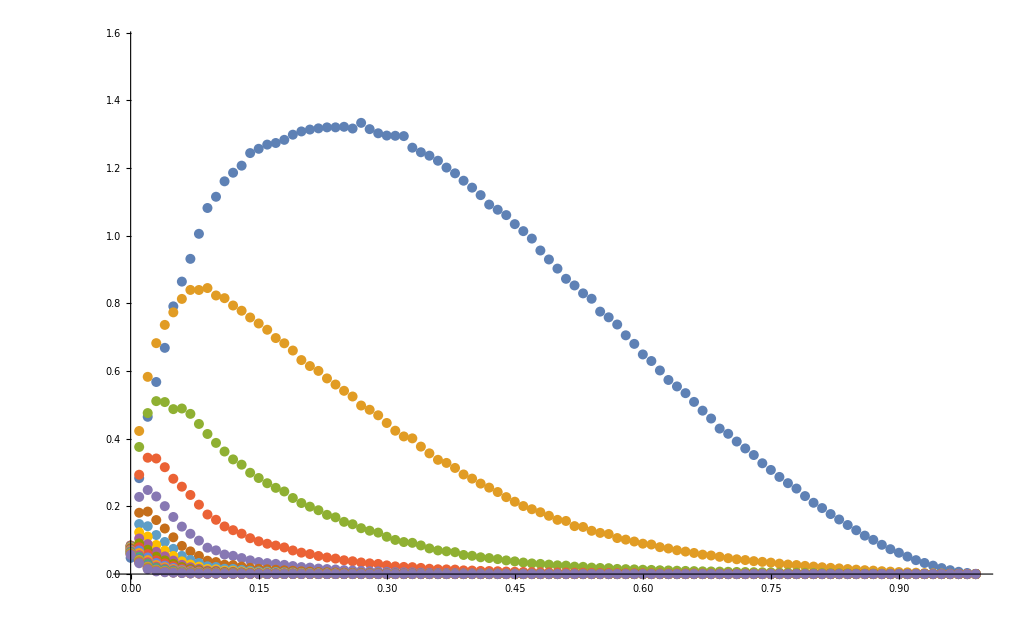

```mathematica
SetDirectory[NotebookDirectory[]]; 
tableSize = 100;
bouncesCount = 20;
rawArray=Table[ BinaryReadList["WallHeight"<>ToString[i]<>".float", "Real32"],{i,1,bouncesCount}];
bounces = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
ListPlot[bounces,PlotRange->{0,π/2}]
```

These were the original curves where I made the mistake of using initial direct illuminance E0 instead of AO to drive the histogram bins storage:

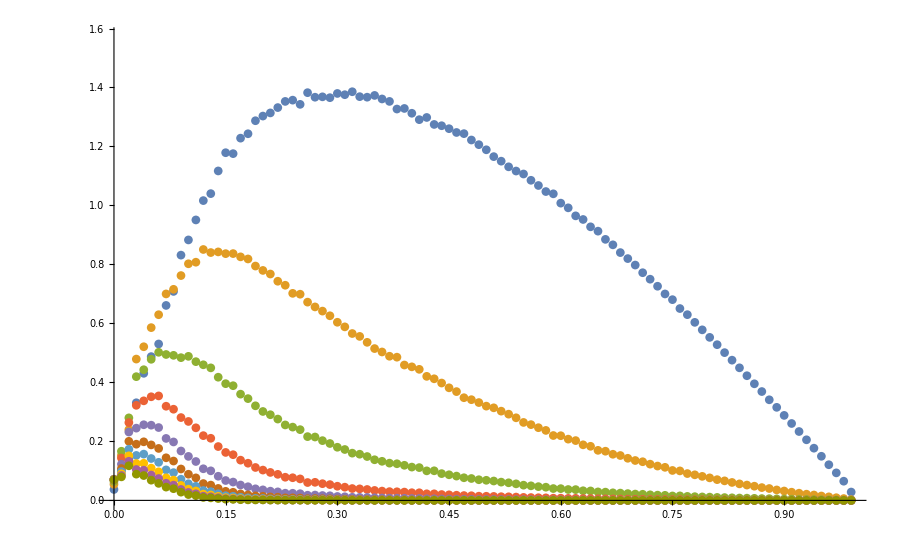

## Summing the Curves

These curves represent

## Starting the Fitting

Intuitively, it looks like a log-normal distribution curve that we can model as f(x)=a*x*(1-x)*e^-bx.
We can see below that it’s actually a very nice fit for the curves and may even deduce a general rule to find a and b coefficients as a function of the bounce index...

```mathematica
Manipulate[Plot[8*x*(1-x)*ⅇ^(-k*x),{x,0,1},PlotRange->{0,π/2}],{{k,1},0,20}]
```

```mathematica
Clear[a,b]
model=b/a*x*(1-x)*Exp[-b*x];
fitter[i_]:=Module[{},
FindFit[bounces[[i]], model,{a,{b,20}},{x}]
]
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}]
```

{{a→0.145266,b→1.55043},{a→0.360125,b→4.9367},{a→0.662865,b→9.62783},{a→1.00588,b→16.3854},{a→1.36116,b→22.712},{a→1.74407,b→27.4423},{a→2.15167,b→31.166},{a→2.57505,b→34.4689},{a→3.00497,b→37.6836},{a→3.43309,b→40.9832}}

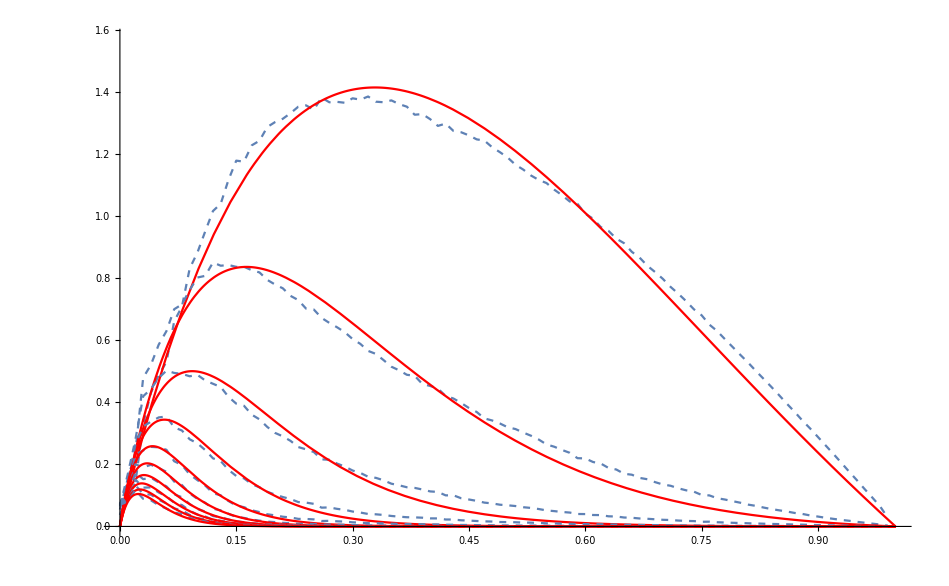

```mathematica
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.fits[[bounceIndex]],{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

Now we plot the various a and b coefficients as a function of the bounce index:

{0.145266,0.360125,0.662865,1.00588,1.36116,1.74407,2.15167,2.57505,3.00497,3.43309}

{1.55043,4.9367,9.62783,16.3854,22.712,27.4423,31.166,34.4689,37.6836,40.9832}

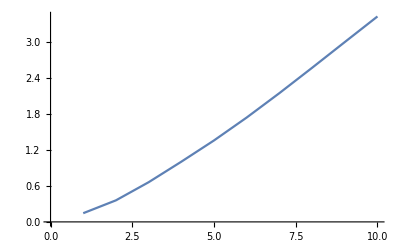

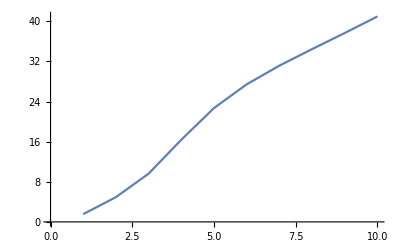

```mathematica
coeffsA=Table[a/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
coeffsB=Table[b/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
ListLinePlot[coeffsA,PlotRange->Full]
ListLinePlot[coeffsB,PlotRange->Full]
```

We notice the curves are almost linear so let’s try and fit the a and b coefficients as a linear function of the bounce index:

{a0→0.,a1→0.251994,a2→0.0130302}

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{b0→1.,b1→1.,b2→1.,b3→1.}

Function[{x},1.55043+3.93698 (-1+x)]

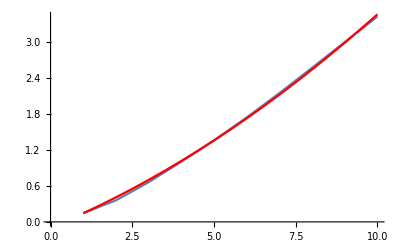

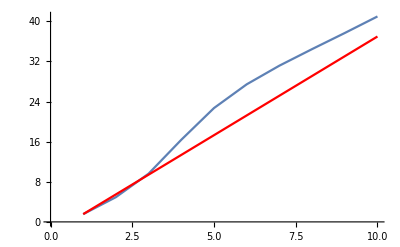

```mathematica
modelA=coeffsA[[1]]+0*a0+a1*(x-1)+a2*(x-1)^2;
modelB=coeffsB[[1]]+0*b0+b1*(x-1)+b2*(x-1)^2+b3*(x-1)^3;
modelB=coeffsB[[1]]+0*b0+b1*(x-1);
modelB=coeffsB[[1]]+(x-1)/(bouncesCount-1)*(coeffsB[[bouncesCount]] - coeffsB[[1]] - 4);
modelFitA=FindFit[coeffsA,modelA,{a0,a1,a2},{x}]
modelFitB=FindFit[coeffsB,modelB,{b0,b1,b2,b3},{x}]
(*Show[ListPlot[coeffsA,PlotRange->Full],Plot[modelA/.modelFitA,{x,0,bouncesCount}]]
Show[ListPlot[coeffsB,PlotRange->Full],Plot[modelB/.modelFitB,{x,0,bouncesCount}]]*)

modelFitA=Function[{x},Evaluate[modelA/.modelFitA]];
modelFitB=Function[{x},Evaluate[modelB/.modelFitB]]
Show[ListLinePlot[coeffsA,PlotRange->Full],Plot[modelFitA[x],{x,1,bouncesCount},PlotStyle->Red]]
Show[ListLinePlot[coeffsB,PlotRange->Full],Plot[modelFitB[x],{x,1,bouncesCount},PlotStyle->Red]]
```

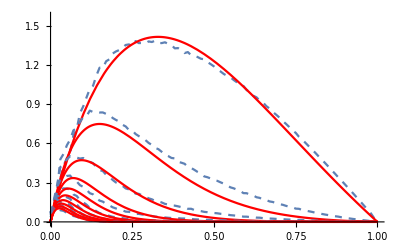

```mathematica
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.{a-> modelFitA[bounceIndex],b-> modelFitB[bounceIndex]},{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

{10.673,13.7083,14.5246,16.2896,16.6857,15.7346,14.4846,13.3858,12.5404,11.9377}

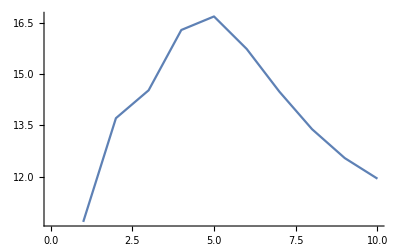

```mathematica
finalCoeffs=Table[coeffsB[[i]]/coeffsA[[i]],{i,1,bouncesCount}]
ListLinePlot[finalCoeffs]
```

## Refitting with Constrained b

Assuming b=?? we can try and re-fit the remaining variable a:

```mathematica
Clear[a,b]
fitter[i_]:=Module[{},
b = modelFitB[i];
FindFit[bounces[[i]], model,{a},{x}]
];
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}];
newCoeffsA=Table[a/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
Clear[a,b]
```

{0.145266,0.354521,0.667576,1.10147,1.56096,1.99283,2.40315,2.80657,3.20964,3.6127}

0.145266+0.385271 (-1+x)

0.145266+a0 (-1+x)+a1 (-1+x)^2

0.145266+a0 (-1+x)+a1 (-1+x)^2+a2 (-1+x)^3

{a0→0.19848,a1→0.048556,a2→-0.00312863}

a0→0.19848

a1→0.024278

{a0→0.19848,a1→0.024278,a2→0.}

Function[{x},0.145266+0.19848 (-1+x)+0.024278 (-1+x)^2]

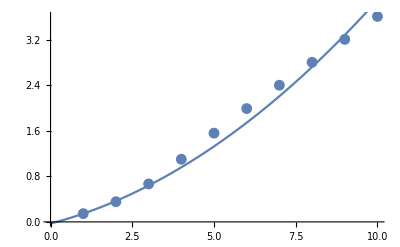

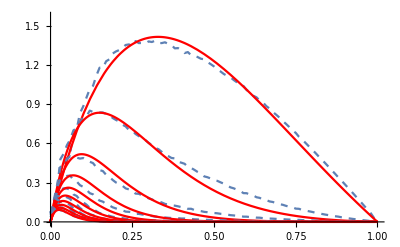

```mathematica
Clear[a0,a1,a2]
modelA=newCoeffsA[[1]]+(x-1)/(bouncesCount-1)*(newCoeffsA[[bouncesCount]]-newCoeffsA[[1]])
modelA=newCoeffsA[[1]]+a0*(x-1)+a1*(x-1)^2
modelA=newCoeffsA[[1]]+a0*(x-1)+a1*(x-1)^2+a2*(x-1)^3
modelFitA=FindFit[newCoeffsA,modelA,{a0,a1,a2},{x}]
modelFitA[[1]]=a0-> 1.0*(a0/.modelFitA[[1]])
modelFitA[[2]]=a1-> 0.5*(a1/.modelFitA[[2]])
modelFitA[[3]]=a2-> 0.0;
modelFitA
modelFitA=Function[{x},Evaluate[modelA/.modelFitA]]
Show[ListPlot[newCoeffsA,PlotRange->Full],Plot[modelFitA[x],{x,0,bouncesCount}]]
Clear[a,b]
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.{ b-> modelFitB[bounceIndex],a->modelFitA[bounceIndex]},{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

Reference graph without manual change of fitting variables (a0,a1,a2):

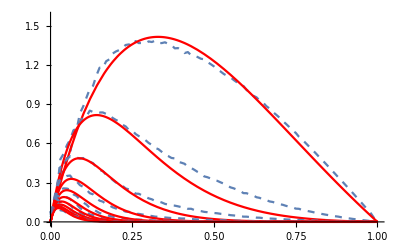

-Graphics-

## Using Fitted Data

Okay so we ended up with these expressions for a and b coefficients depending on i, the bounce index:
	a=0.145266+0.19848 (i-1)+0.024278 (i-1)^2
	b=1.55043+3.93698 (i-1)

We plug these into the reflectance model depending on α=AO/π:
	f(α,i)=b/a*α*(1-α)*ⅇ^(-b α)

As agreed, we assume the surface albedo ρ is constant in the surrounding of the luminance estimate and we can compute the final luminance due to indirect bounce on the surface as:

	L_indirect(x,ω_o) = 1/π[ρ AO(x) + ∑_(i=1)^N ρ^i f((AO(x))/π,i)]  E(x)

We notice the interesting property of albedo saturation as the amount of bounces increases.

## Verifying

We open the experimental ρ = 0.5 curves:

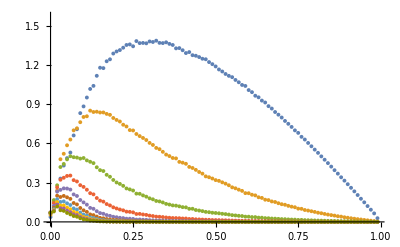

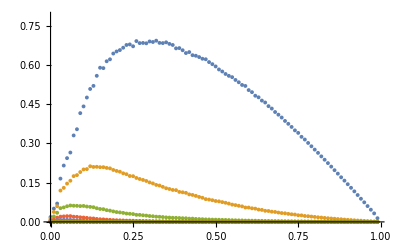

```mathematica
rawArray05=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.5.float", "Real32"],{i,1,bouncesCount}];
bounces05 = Table[Table[{(i-1)/tableSize,rawArray05[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
ListPlot[bounces,PlotRange->{0,π/2}]
ListPlot[bounces05,PlotRange->{0,π/4}]
```

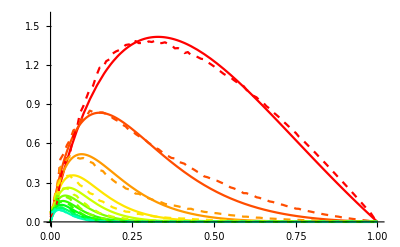

```mathematica
a[i_]:=0.14526642906187737+0.1984799936582921 (i-1)+0.024277999559107394 (i-1)^2
b[i_]:=1.5504282580946984+3.936979219376581 (i-1)
f[α_,i_]:=b[i]/a[i] α(1-α)ⅇ^(-b[i]α)
Show[Table[Plot[f[x,i],{x,0,1},PlotRange->{{0,1},{0,π/2}},PlotStyle->Hue[(i-1)/20]],{i,1,10}],
Table[ListLinePlot[bounces[[i]],PlotRange->Full,PlotStyle->{Dashed,Hue[(i-1)/20]}],{i,1,10}]]
```

And now for the moment of truth:

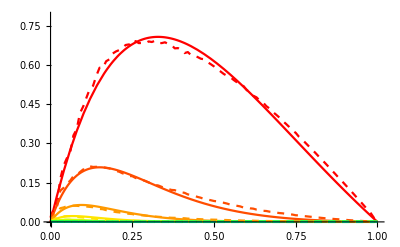

```mathematica
ρ=0.5;
Show[Table[Plot[ρ^i* f[x,i],{x,0,1},PlotRange->{{0,1},{0,π/4}},PlotStyle->Hue[(i-1)/20]],{i,1,10}],
Table[ListLinePlot[bounces05[[i]],PlotRange->Full,PlotStyle->{Dashed,Hue[(i-1)/20]}],{i,1,10}]]
```

## Let’s try and model a bounce function from its predecessor

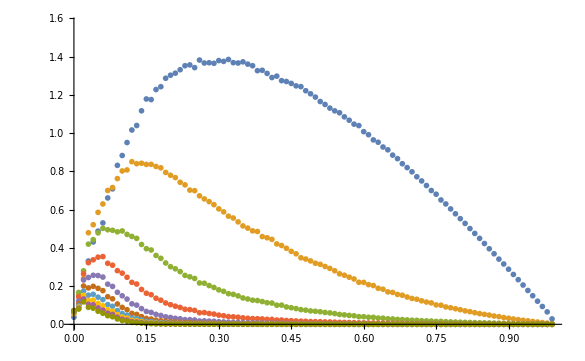

```mathematica
ListPlot[bounces,PlotRange->{0,π/2}]
```

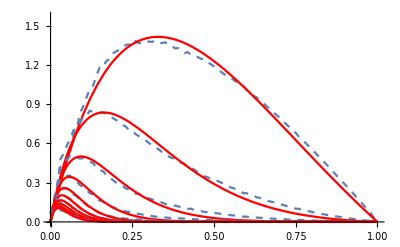

```mathematica
Clear[a,b]
model=b/a*x*(1-x)*Exp[-b*x];
fitter[i_]:=Module[{},
FindFit[bounces[[i]], model,{a,{b,20}},{x}]
]
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}];
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.fits[[bounceIndex]],{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

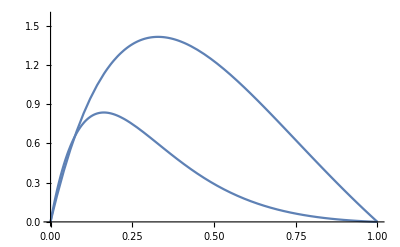

```mathematica
(* Build initial bounce function *)
f1=Function[{x},model/.fits[[1]]];
f2=Function[{x},model/.fits[[2]]];
Show[Plot[f1[x],{x,0,1},PlotRange->{0,π/2}],
Plot[f2[x],{x,0,1},PlotRange->{0,π/2}]]
(* Find how much f2 can be deduced from f1 by multiplying by an exponential *)
```

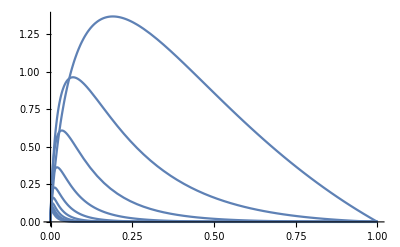

```mathematica
evals=Table[model/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}];
functor[i_]:=Module[{},
Function[{x},evals[[i]]]
]
funcs=Table[functor[bounceIndex],{bounceIndex,1,bouncesCount}];
Plot[funcs[[2]][x],{x,0,1}];
Show[Table[Plot[evals[[i]]/.x-> t,{t,0,1},PlotRange->All],{i,1,10}]];
Show[Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,1,10}]]
```

{a→1.28439,b→3.38627}

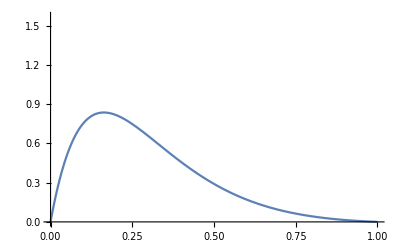

```mathematica
divModel=f1[x]*a*Exp[-b*x];
fit2=FindFit[bounces[[2]], divModel,{a,{b,20}},{x}]
fact2=Function[{x},divModel/.fit2];
Plot[fact2[x],{x,0,1},PlotRange->{0,π/2}]
```

{a→1.28439,b→3.38627}

{{a→1.28439,b→3.38627},{a→1.05955,b→4.69113},{a→1.12152,b→6.75756},{a→1.02432,b→6.32656},{a→0.942998,b→4.73031},{a→0.920554,b→3.72372},{a→0.924139,b→3.30294},{a→0.936848,b→3.21469},{a→0.951939,b→3.29962}}

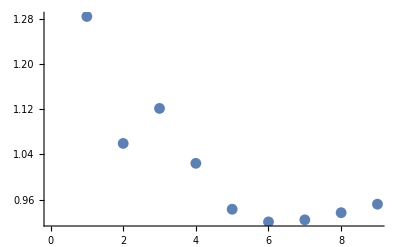

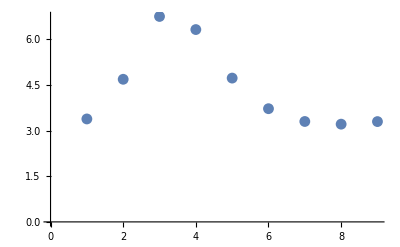

```mathematica
divModel=fprev*a*Exp[-b*x];
divFit=FindFit[bounces[[2]], divModel/.{fprev->f1[x]},{a,{b,1}},{x}]
divCoeffs=Table[FindFit[bounces[[bounceIndex]], divModel/.{fprev->funcs[[bounceIndex-1]][x]},{a,{b,20}},{x}],{bounceIndex,2,bouncesCount}]
ListPlot[a/.divCoeffs]
ListPlot[b/.divCoeffs]
```

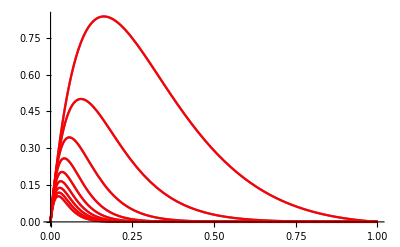

```mathematica
Show[
Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,2,bouncesCount}],
Table[Plot[funcs[[i-1]][x]*(a*Exp[-b*x]/.divCoeffs[[i-1]]),{x,0,1},PlotStyle->Red,PlotRange->All],{i,2,bouncesCount}]
]
```

Let’s fix b to a constant so we’re left with multiplying by a constant exponential value and coefficient a:

4.38

4.

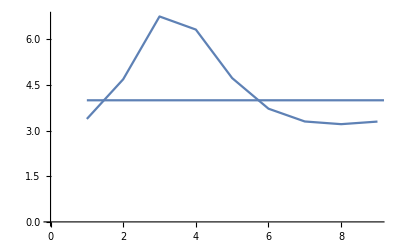

```mathematica
Clear[h]
defB = h/.FindFit[b/.divCoeffs,h,{h},{x}];
defB = 4.38
defB = 4.0
Show[ListLinePlot[b/.divCoeffs,PlotRange->All],Plot[defB,{x,1,bouncesCount},PlotRange->All]]
```

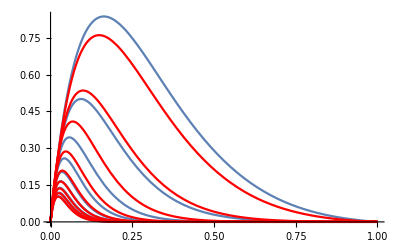

```mathematica
Show[
Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,2,bouncesCount}],
Table[Plot[funcs[[i-1]][x]*(a*Exp[-defB*x]/.divCoeffs[[i-1]]),{x,0,1},PlotStyle->Red,PlotRange->All],{i,2,bouncesCount}]
]
```

We see that now the amplitude coefficients a are a bit off so we need to recompute them with fixed factor b:

{{a→0.680573},{a→1.04274},{a→1.16286},{a→1.14321},{a→1.10282},{a→1.0725},{a→1.05111},{a→1.03584},{a→1.0248}}

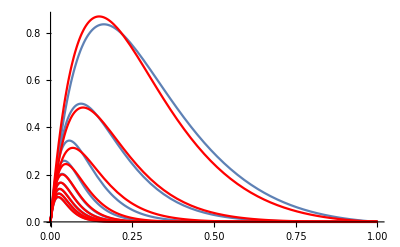

```mathematica
divModel=fprev*1/a*Exp[-defB*x];
divCoeffsA=Table[FindFit[bounces[[bounceIndex]], divModel/.{fprev->funcs[[bounceIndex-1]][x]},{a},{x}],{bounceIndex,2,bouncesCount}]
Show[
Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,2,bouncesCount}],
Table[Plot[funcs[[i-1]][x]*(1/a*Exp[-defB*x]/.divCoeffsA[[i-1]]),{x,0,1},PlotStyle->Red,PlotRange->All],{i,2,bouncesCount}]
]
```

{a→0.992275,b→0.60397,c→0.452188}

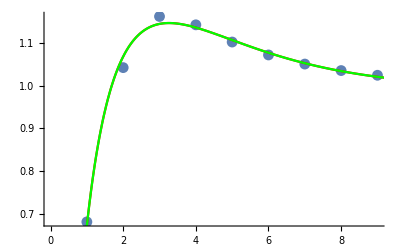

```mathematica
logModel=a;
logModel=a+Log[b*x]*Exp[-c*x];
logFit=FindFit[a/.divCoeffsA,logModel,{{a,1},{b,1,0.1,10},{c,1}},{x}]
glamour=Function[{x},logModel/.logFit];
Show[
ListPlot[a/.divCoeffsA,PlotRange->All],
Plot[logModel/.logFit,{x,0,10},PlotRange->All,PlotStyle->Red],
Plot[glamour[x],{x,0,10},PlotRange->All,PlotStyle->Green]
]
```

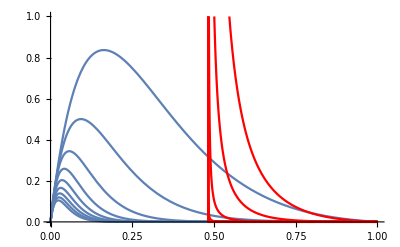

```mathematica
Show[
Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,2,bouncesCount}],
Table[Plot[funcs[[i-1]][x]*(Exp[-defB*x]/glamour[i-1]),{x,0,1},PlotStyle->Red,PlotRange->{{0,10},{0,1}}],{i,2,bouncesCount}]
]
```

## Shifting Perspective

What if we tried to use the initial f1 curve’s coefficient over itself multiple times, as we’ll certainly do it in code?
That requires shifting the curves on themselves:

```mathematica
ta=Table[ funcs[[i]][1]/.x-> 0.5,{i,1,bouncesCount}];
ListLinePlot[ta,PlotRange->{{0,10},{0,π/2}}];
```

```mathematica
Manipulate[ListLinePlot[Table[ funcs[[i]][1]/.x-> t ,{i,1,bouncesCount}],PlotRange->{{1,10},{0,π/2}}],{{t,0.5},0,1}]
```

```mathematica
bouncesCount=8;
ta3D=Table[Table[ funcs[[i]][1]/.x-> t/100,{i,1,bouncesCount}],{t,0,100}];
ta3D=Table[Table[ (funcs[[i]][1]/.x-> t/100)/(t/100*(1-t/100)),{i,1,bouncesCount}],{t,10,99}];
ListPlot3D[ta3D,PlotRange->All,AxesLabel->{"Bounce Index","100*AO","Normalized Irradiance"}]
```

-Graphics3D-

Intuively, removing the α(1-α) shows us some sort of regular exponential decay whose decay rate is correlated to α as well...
Let’s try and see if that’s also the case with the original curves:

```mathematica
ta3D=Table[ Table[bounces[[i]][[j]][[2]],{j,1,100}],{i,1,bouncesCount}];
ta3D=Table[Table[ (bounces[[i]][[j]][[2]])/Max[0.01,(j-1)/99*(1-(j-1)/99)],{i,1,bouncesCount}],{j,1,100}];
MatrixForm[ta3D];
ListPlot3D[ta3D,PlotRange->All,AxesLabel->{"Bounces","α","Amplitude"}]
```

-Graphics3D-

Let’s try and fit the initial bounce value with an exponential:

{{1/11,10.062},{19/99,8.30058},{29/99,6.59232},{13/33,5.56611},{49/99,4.8249},{59/99,4.31694},{23/33,3.88192},{79/99,3.58703},{89/99,3.47447}}

{a→12.255,b→-26.1448,c→27.5502,d→-10.4155}

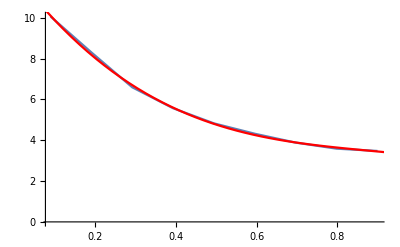

```mathematica
Clear[α,x]
modelA0=9.239635202619764*Exp[-b*(α-1)];
modelA0=a*Exp[-b*α];
modelA0=a+b*α+c*α^2+d*α^3;
samplesCount=Length[ta3D];
coeffsA0=Table[{(i-1)/(samplesCount-1),ta3D[[i]][[1]]},{i,10,90,10}]
fitA0=FindFit[coeffsA0,modelA0,{a,b,c,d},{α}]
fA0=Function[{α},modelA0/.fitA0];
Show[
ListLinePlot[coeffsA0,PlotRange->All],
Plot[fA0[α],{α,0,1},PlotRange->All,PlotStyle->Red]
]
```

Now let’s find a rule to drive the decay factor as a function of α :

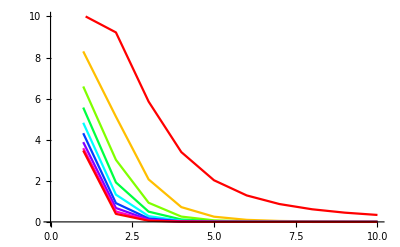

```mathematica
ta3Dortho=Transpose@ta3D;
Show[Table[ListLinePlot[ta3D[[sampleIndex]],PlotRange->{0,10},PlotStyle->Hue[(sampleIndex-10)/80]],{sampleIndex,10,90,10}]]
```

{6.59232,3.02221,0.931351,0.258434,0.0757342,0.0261872,0.0112131,0.00586212,0.00356892,0.00240701}

6.6099

6.6099 ⅇ^(-b (-1+x))

{a→1.,b→0.887286}

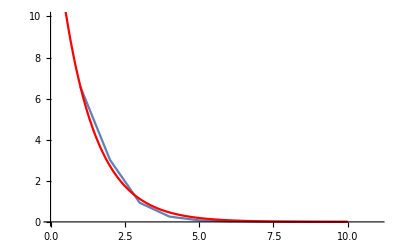

```mathematica
α=0.3;
sampleIndex=Round[α*samplesCount];
ta3D[[sampleIndex]]
A0=fA0[α]
modelDecay=A0*Exp[-b*(x-1)];
modelDecay=fA0[α]*Exp[-b*(x-1)]
fitDecay=FindFit[ta3D[[sampleIndex]],modelDecay,{a,b},{x}]
fDecay=Function[{x},modelDecay/.fitDecay];
Show[
ListLinePlot[ta3D[[sampleIndex]],PlotRange->{{0,11},{0,bouncesCount}}],
Plot[modelDecay/.fitDecay/.x-> bounceIndex,{bounceIndex,0,bouncesCount},PlotRange->Full,PlotStyle->Red]
]
```

Applying to many samples, we get a list of coefficients depending on α

{{x→0.1,a→9.90564,b→0.332558},{x→0.15,a→8.91804,b→0.493305},{x→0.2,a→8.04476,b→0.641783},{x→0.25,a→7.27798,b→0.775267},{x→0.3,a→6.6099,b→0.887286},{x→0.35,a→6.0327,b→1.00709},{x→0.4,a→5.53856,b→1.11093},{x→0.45,a→5.11968,b→1.20334},{x→0.5,a→4.76825,b→1.31264},{x→0.55,a→4.47646,b→1.40085},{x→0.6,a→4.23648,b→1.54751},{x→0.65,a→4.04052,b→1.62502},{x→0.7,a→3.88076,b→1.75134},{x→0.75,a→3.74938,b→1.84375},{x→0.8,a→3.63858,b→1.97268},{x→0.85,a→3.54054,b→2.0899},{x→0.9,a→3.44746,b→2.1728}}

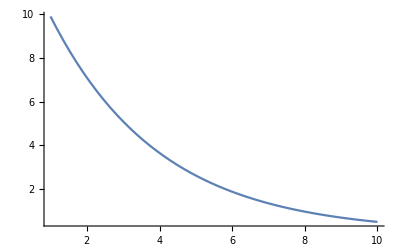

```mathematica
Clear[a,b]
fitter[α_]:=Module[{},
sampleIndex=Round[α*samplesCount];
A0=fA0[α];
modelDecay=A0*Exp[-b*(x-1)];
{x->α,a-> A0, FindFit[ta3D[[sampleIndex]],modelDecay,{b},{x}][[1]]}
]
fitsDecay=Table[fitter[α],{α,0.1,0.9,0.05}]
Plot[a*Exp[-b*(x-1)]/.fitsDecay[[1]],{x,1,bouncesCount},PlotRange->Full]
```

{{0.1,0.332558},{0.15,0.493305},{0.2,0.641783},{0.25,0.775267},{0.3,0.887286},{0.35,1.00709},{0.4,1.11093},{0.45,1.20334},{0.5,1.31264},{0.55,1.40085},{0.6,1.54751},{0.65,1.62502},{0.7,1.75134},{0.75,1.84375},{0.8,1.97268},{0.85,2.0899},{0.9,2.1728}}

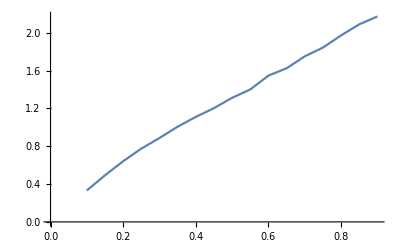

```mathematica
coeffsDecay={x,b}/.fitsDecay
ListLinePlot[coeffsDecay]
```

It looks a lot (!!) like a linear fit! <3

{a→0.186195,b→2.23562}

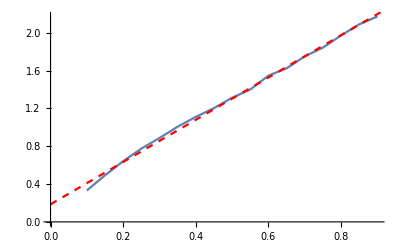

```mathematica
Clear[a,b,α]
modelCoeffsDecay=a+b*α;
fitCoeffsDecay=FindFit[coeffsDecay,modelCoeffsDecay,{a,b},{α}]
Show[
ListLinePlot[coeffsDecay],
Plot[modelCoeffsDecay/.fitCoeffsDecay,{α,0,1},PlotStyle->{Red,Dashed}]
]
```

## Putting it all together!

Okay so now it looks like we have it all: each curve for each bounce i is of the form f_i(α)=A_i*α*(1-α)*e^-B_iα as stated at the beginning of the document.
We later tried to shift our perspective to see, for a given α=AO/π, the shape of the curve we get for each new bounce and it looks like a simple exponential g(α,i)=A(α)ⅇ^(-B(α)i) with an initial amplitude A(α) and a decay factor B(α).
A very good fit for A(α)=12.255-26.1448α+27.5502 α^2-10.4155 α^3 that allows us to find a very simple linear fit for B(α)=0.186195+2.23562α

```mathematica
Clear[A,B]
A[α_]:=12.255-26.144751371564944α+27.5502 α^2-10.4155 α^3
B[α_]:=0.18619452933736622+2.235617876545042α
```

```mathematica
Manipulate[Plot[A[α]*Exp[-B[α]*x],{x,1,10},PlotRange->{0,10}],{{α,0},0,1}]
```

Let’s verify the curves fit our experimental data:

```mathematica
Manipulate[
Show[
ListLinePlot[ta3D[[Round[1+100*α]]],PlotRange->{0,10}],
Plot[A[α]*Exp[-B[α]*(x-1)],{x,1,10},PlotRange->{0,10},PlotStyle->Red]
],{{α,0.2},0,1}]
```

Now, we re-plot the entire data and final curves, with the attenuation curve:

```mathematica
(*finalTable3D=Table[Table[ (bounces[[i]][[j]][[2]])/Max[0.01,(j-1)/99*(1-(j-1)/99)],{i,1,bouncesCount}],{j,1,100}];*)
finalTable3D=Table[Table[ bounces[[i]][[j]][[2]],{i,1,bouncesCount}],{j,1,100}];
reconstructedTable3D=Table[Table[ α*(1-α)*A[α]*Exp[-B[α]*(i-1)],{i,1,bouncesCount}],{α,0,1,0.01}];
Show[ListPlot3D[finalTable3D,PlotRange->{0,π/2},AxesLabel->{"Bounces","α","Amplitude"}],
ListPlot3D[reconstructedTable3D,PlotRange->{0,π/2},AxesLabel->{"Bounces","α","Amplitude"},PlotStyle->Red]]
```

-Graphics3D-

So basically, in the shader, all we need to do is computing α=AO/π A_0=α(1-α)A(α) and K=ρ.ⅇ^(-B(α)) then the final expression for outgoing luminance is given by:

	 L(x,ω_o)=(ρ/π.AO +A_0/π ∑_(i=1)^∞ K^i )E(x)=(ρ/π.AO +A_0/π K/(1-K) )E(x)  since K<1

```mathematica
Manipulate[
A0=A[α];
K0=Exp[-B[α]];
Show[
ListPlot[Table[α*(1-α)*A0*Product[K0,{i,maxI}],{maxI,1,bouncesCount}],PlotRange->{0,π/4}],
Plot[α*(1-α)*A0*Exp[-B[α]*x],{x,1,10},PlotRange->All,PlotStyle->Red]
],{{α,0.1},0,1}]
```

Final verification with the 50% albedo table:

```mathematica
ρ=0.5;
finalTable3D=Table[Table[ bounces05[[i]][[j]][[2]],{i,1,bouncesCount}],{j,1,100}];
reconstructedTable3D=Table[Table[ α*(1-α)*A[α]*ρ^i*Exp[-B[α]*(i-1)],{i,1,bouncesCount}],{α,0,1,0.01}];
Show[ListPlot3D[finalTable3D,PlotRange->{0,π/4},AxesLabel->{"Bounces","α","Amplitude"}],
ListPlot3D[reconstructedTable3D,AxesLabel->{"Bounces","α","Amplitude"},PlotStyle->Red]]
```

-Graphics3D-

```mathematica
Clear[ρ,b]
ρ=0.5;
b=0.2;
K0=ρ*ⅇ^-b;
Sum[K0^x,{x,1,∞}]
K0/(1-K0)
```

0.693094

0.693094

```mathematica
ρ=1.0;
(*linearTable=Table[(i-1)/tableSize,{i,1,tableSize}];
sumTable=Sum[1/π ρ^i*bounces[[i]],{i,1,bouncesCount}];
finalTable=Table[{(i-1)/tableSize,(i-1)/tableSize+sumTable[[i]][[2]]},{i,1,tableSize}];*)
Manipulate[
sumTable=ρ*bounces[[1]]+(ρ/π)^2*bounces[[2]]+(ρ/π)^3*bounces[[3]]+(ρ/π)^4*bounces[[4]]+ρ^5*bounces[[5]]+ρ^6*bounces[[6]]+ρ^7*bounces[[7]];
sumTable=Sum[(ρ/1)^i*bounces[[i]],{i,1,bouncesCount}];
finalTable=Table[{(i-1)/tableSize,(i-1)/tableSize+1/π sumTable[[i]][[2]]},{i,1,tableSize}];
ListLinePlot[finalTable,PlotRange->{0,1.1}],{{ρ,0.1},0,1}]
```

Building the final expression to obtain the same kind of curve as the one in Jimenez’s paper:

```mathematica
Manipulate[Plot[α+1/π α*(1-α)*A[α]*(ρ*Exp[-B[α]])/(1-ρ*Exp[-B[α]]),{α,0,1},PlotRange->{0,1},PlotStyle->Red],{{ρ,0.1},0,1}]
```

Part::partw: Part 10 of {{a → 0.680573}, {a → 1.04274}, {a → 1.16286}, {a → 1.14321}, {a → 1.10282}, {a → 1.0725}, {a → 1.05111}, {a → 1.03584}, {a → 1.0248}} does not exist.

ReplaceAll::reps: {{{a → 0.680573}, {a → 1.04274}, {a → 1.16286}, {a → 1.14321}, {a → 1.10282}, {a → 1.0725}, {a → 1.05111}, {a → 1.03584}, {a → 1.0248}} ⟦ 10 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

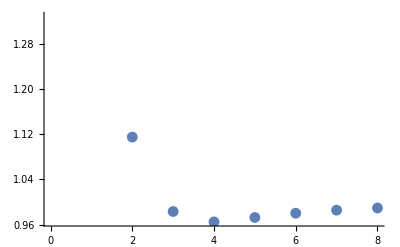

```mathematica
ListPlot[Table[(a/.divCoeffsA[[i]])/(a/.divCoeffsA[[i-1]]),{i,2,bouncesCount}]]
```

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.054395},{1/100,0.152475},{1/50,0.239881},{3/100,0.479152},{1/25,0.520947},{1/20,0.585763},{3/50,0.629567},{7/100,0.700074},{2/25,0.715666},{9/100,0.762299},{1/10,0.802291},{11/100,0.807603},{3/25,0.850698},{13/100,0.840319},{7/50,0.842531},{3/20,0.83661},{4/25,0.836818},{17/100,0.82575},{9/50,0.818634},{19/100,0.794592},{1/5,0.779717},{21/100,0.767559},{11/50,0.743065},{23/100,0.729495},{6/25,0.702015},{1/4,0.699104},{13/50,0.672219},{27/100,0.656018},{7/25,0.641828},{29/100,0.625966},{3/10,0.603964},{31/100,0.588366},{8/25,0.56578},{33/100,0.556027},{17/50,0.535956},{7/20,0.514761},{9/25,0.503237},{37/100,0.488762},{19/50,0.485569},{39/100,0.459003},{2/5,0.452825},{41/100,0.444365},{21/50,0.420585},{43/100,0.412303},{11/25,0.397904},{9/20,0.381721},{23/50,0.368878},{47/100,0.348123},{12/25,0.341466},{49/100,0.33173},{1/2,0.319601},{51/100,0.313889},{13/25,0.302581},{53/100,0.29237},{27/50,0.280077},{11/20,0.264326},{14/25,0.256872},{57/100,0.246509},{29/50,0.237268},{59/100,0.219962},{3/5,0.219278},{61/100,0.207675},{31/50,0.202776},{63/100,0.18844},{16/25,0.183443},{13/20,0.169733},{33/50,0.166748},{67/100,0.156425},{17/25,0.152156},{69/100,0.142797},{7/10,0.135249},{71/100,0.131059},{18/25,0.122857},{73/100,0.116432},{37/50,0.112112},{3/4,0.101487},{19/25,0.0999895},{77/100,0.0909519},{39/50,0.0867397},{79/100,0.0814425},{4/5,0.0763704},{81/100,0.0703441},{41/50,0.0662323},{83/100,0.060832},{21/25,0.056012},{17/20,0.0519434},{43/50,0.048115},{87/100,0.0434114},{22/25,0.0402554},{89/100,0.0354001},{9/10,0.0318146},{91/100,0.027814},{23/25,0.0243905},{93/100,0.0210489},{47/50,0.0182812},{19/20,0.0149027},{24/25,0.0120484},{97/100,0.00907089},{49/50,0.0061625},{99/100,0.00257255}},(2.1346 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}]

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, « 3 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0., 0.054395}, {0.01, 0.152475}, {0.02, 0.239881}, {0.03, 0.479152}, {0.04, 0.520947}, {0.05, 0.585763}, {0.06, 0.629567}, {0.07, 0.700074}, {0.08, 0.715666}, {0.09, 0.762299}, {0.1, 0.802291}, {0.11, 0.807603}, « 27 », {0.39, 0.459003}, {0.4, 0.452825}, {0.41, 0.444365}, {0.42, 0.420585}, {0.43, 0.412303}, {0.44, 0.397904}, {0.45, 0.381721}, {0.46, 0.368878}, {0.47, 0.348123}, {0.48, 0.341466}, {0.49, 0.33173}, « 50 »}, « 2 », {0.0000204286}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

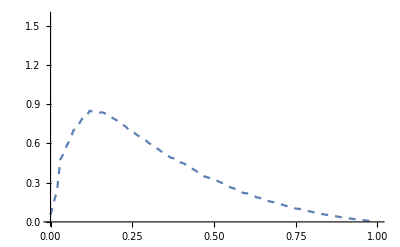

```mathematica
f1=Function[{x},model/.fits[[1]]];
Plot[f1[x],{x,0,1}];
model2=f1[x]*b/a*Exp[-b*x];
fit2=FindFit[bounces[[2]],model2,{a,b},{x}]
f2=Function[{x},model2/.fit2];
Show[
ListLinePlot[bounces[[2]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[f2[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, « 18 »\ « 3 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.0644934},{1/100,0.166616},{1/50,0.279836},{3/100,0.419506},{1/25,0.443042},{1/20,0.478397},{3/50,0.502134},{7/100,0.494698},{2/25,0.491835},{9/100,0.483957},{1/10,0.488438},{11/100,0.470398},{3/25,0.459806},{13/100,0.44938},{7/50,0.417658},{3/20,0.395725},{4/25,0.388853},{17/100,0.360218},{9/50,0.345068},{19/100,0.320713},{1/5,0.301487},{21/100,0.29047},{11/50,0.275746},{23/100,0.255856},{6/25,0.24846},{1/4,0.239832},{13/50,0.216226},{27/100,0.2149},{7/25,0.202604},{29/100,0.192903},{3/10,0.180191},{31/100,0.172548},{8/25,0.160178},{33/100,0.156579},{17/50,0.148714},{7/20,0.137779},{9/25,0.132527},{37/100,0.126295},{19/50,0.124248},{39/100,0.119022},{2/5,0.112911},{41/100,0.111181},{21/50,0.100149},{43/100,0.100375},{11/25,0.0907993},{9/20,0.0868527},{23/50,0.0823923},{47/100,0.0767546},{12/25,0.074217},{49/100,0.0700358},{1/2,0.0681404},{51/100,0.0657395},{13/25,0.0619384},{53/100,0.0596653},{27/50,0.0561079},{11/20,0.0516134},{14/25,0.0494036},{57/100,0.0466142},{29/50,0.0447192},{59/100,0.0401356},{3/5,0.0398435},{61/100,0.0368706},{31/50,0.0365578},{63/100,0.0326591},{16/25,0.0320426},{13/20,0.0287873},{33/50,0.0279825},{67/100,0.0256719},{17/25,0.0247106},{69/100,0.0230628},{7/10,0.0214108},{71/100,0.0207132},{18/25,0.0189188},{73/100,0.0178012},{37/50,0.017209},{3/4,0.0150282},{19/25,0.0152946},{77/100,0.0135314},{39/50,0.0126362},{79/100,0.011726},{4/5,0.0110713},{81/100,0.0101247},{41/50,0.00952724},{83/100,0.00874461},{21/25,0.00802355},{17/20,0.00754802},{43/50,0.00695417},{87/100,0.00617516},{22/25,0.00580952},{89/100,0.00503901},{9/10,0.00449074},{91/100,0.00392841},{23/25,0.0034301},{93/100,0.00295668},{47/50,0.00259861},{19/20,0.00207451},{24/25,0.00169034},{97/100,0.00126655},{49/50,0.000861621},{99/100,0.000360172}},1/a 0.2 ⅇ^(-0.2 x) ((2.1346 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.054395},{1/100,0.152475},{1/50,0.239881},{3/100,0.479152},{1/25,0.520947},{1/20,0.585763},{3/50,0.629567},{7/100,0.700074},{2/25,0.715666},{9/100,0.762299},{1/10,0.802291},{11/100,0.807603},{3/25,0.850698},{13/100,0.840319},{7/50,0.842531},{3/20,0.83661},{4/25,0.836818},{17/100,0.82575},{9/50,0.818634},{19/100,0.794592},{1/5,0.779717},{21/100,0.767559},{11/50,0.743065},{23/100,0.729495},{6/25,0.702015},{1/4,0.699104},{13/50,0.672219},{27/100,0.656018},{7/25,0.641828},{29/100,0.625966},{3/10,0.603964},{31/100,0.588366},{8/25,0.56578},{33/100,0.556027},{17/50,0.535956},{7/20,0.514761},{9/25,0.503237},{37/100,0.488762},{19/50,0.485569},{39/100,0.459003},{2/5,0.452825},{41/100,0.444365},{21/50,0.420585},{43/100,0.412303},{11/25,0.397904},{9/20,0.381721},{23/50,0.368878},{47/100,0.348123},{12/25,0.341466},{49/100,0.33173},{1/2,0.319601},{51/100,0.313889},{13/25,0.302581},{53/100,0.29237},{27/50,0.280077},{11/20,0.264326},{14/25,0.256872},{57/100,0.246509},{29/50,0.237268},{59/100,0.219962},{3/5,0.219278},{61/100,0.207675},{31/50,0.202776},{63/100,0.18844},{16/25,0.183443},{13/20,0.169733},{33/50,0.166748},{67/100,0.156425},{17/25,0.152156},{69/100,0.142797},{7/10,0.135249},{71/100,0.131059},{18/25,0.122857},{73/100,0.116432},{37/50,0.112112},{3/4,0.101487},{19/25,0.0999895},{77/100,0.0909519},{39/50,0.0867397},{79/100,0.0814425},{4/5,0.0763704},{81/100,0.0703441},{41/50,0.0662323},{83/100,0.060832},{21/25,0.056012},{17/20,0.0519434},{43/50,0.048115},{87/100,0.0434114},{22/25,0.0402554},{89/100,0.0354001},{9/10,0.0318146},{91/100,0.027814},{23/25,0.0243905},{93/100,0.0210489},{47/50,0.0182812},{19/20,0.0149027},{24/25,0.0120484},{97/100,0.00907089},{49/50,0.0061625},{99/100,0.00257255}},(2.1346 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}]),{a,0.2},{x}]

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, « 3 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, « 3 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.0644934}, {1/100, 0.166616}, {1/50, 0.279836}, {3/100, 0.419506}, {1/25, 0.443042}, {1/20, 0.478397}, {3/50, 0.502134}, {7/100, 0.494698}, {2/25, 0.491835}, {9/100, 0.483957}, {1/10, 0.488438}, {11/100, 0.470398}, {3/25, 0.459806}, « 26 », {39/100, 0.119022}, {2/5, 0.112911}, {41/100, 0.111181}, {21/50, 0.100149}, {43/100, 0.100375}, {11/25, 0.0907993}, {9/20, 0.0868527}, {23/50, 0.0823923}, {47/100, 0.0767546}, {12/25, 0.074217}, {49/100, 0.0700358}, « 50 »}, « 1 »/a, « 1 », {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

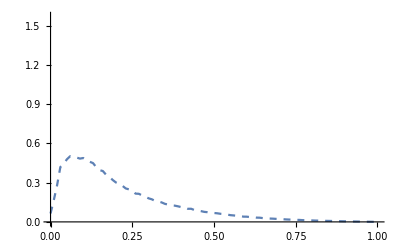

```mathematica
model3=f2[x]*b/a*Exp[-b*x];
fit3=FindFit[bounces[[3]],model3,{a,b},{x}]
f3=Function[{x},model3/.fit3];
Show[
ListLinePlot[bounces[[3]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[f3[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, « 18 »\ « 3 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.0644934}, {1/100, 0.166616}, {1/50, 0.279836}, {3/100, 0.419506}, {1/25, 0.443042}, {1/20, 0.478397}, {3/50, 0.502134}, {7/100, 0.494698}, {2/25, 0.491835}, {9/100, 0.483957}, {1/10, 0.488438}, {11/100, 0.470398}, {3/25, 0.459806}, « 26 », {39/100, 0.119022}, {2/5, 0.112911}, {41/100, 0.111181}, {21/50, 0.100149}, {43/100, 0.100375}, {11/25, 0.0907993}, {9/20, 0.0868527}, {23/50, 0.0823923}, {47/100, 0.0767546}, {12/25, 0.074217}, {49/100, 0.0700358}, « 50 »}, « 1 »/a, {a, « 4 »}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.0693927},{1/100,0.143651},{1/50,0.26385},{3/100,0.322373},{1/25,0.337571},{1/20,0.35135},{3/50,0.354244},{7/100,0.319268},{2/25,0.309136},{9/100,0.280834},{1/10,0.267669},{11/100,0.246085},{3/25,0.219542},{13/100,0.21063},{7/50,0.182554},{3/20,0.162658},{4/25,0.154918},{17/100,0.136437},{9/50,0.126039},{19/100,0.111606},{1/5,0.102752},{21/100,0.094796},{11/50,0.0883583},{23/100,0.0785198},{6/25,0.0767917},{1/4,0.0728438},{13/50,0.0605793},{27/100,0.0613124},{7/25,0.0566535},{29/100,0.0535274},{3/10,0.0480256},{31/100,0.0448069},{8/25,0.0401872},{33/100,0.039103},{17/50,0.0369998},{7/20,0.0337637},{9/25,0.031536},{37/100,0.0296872},{19/50,0.0292039},{39/100,0.0281648},{2/5,0.0260071},{41/100,0.025835},{21/50,0.0223387},{43/100,0.0223038},{11/25,0.0198382},{9/20,0.018868},{23/50,0.0175116},{47/100,0.0163779},{12/25,0.0157751},{49/100,0.0142339},{1/2,0.0139511},{51/100,0.0134869},{13/25,0.012514},{53/100,0.012168},{27/50,0.0112447},{11/20,0.0101705},{14/25,0.00962273},{57/100,0.00904694},{29/50,0.00857343},{59/100,0.00751649},{3/5,0.00758899},{61/100,0.0068866},{31/50,0.0070021},{63/100,0.00613189},{16/25,0.00596792},{13/20,0.0053878},{33/50,0.00520242},{67/100,0.00470617},{17/25,0.00454719},{69/100,0.00426061},{7/10,0.00383446},{71/100,0.00370982},{18/25,0.00339143},{73/100,0.00317931},{37/50,0.00308498},{3/4,0.00268804},{19/25,0.00278149},{77/100,0.00240284},{39/50,0.00222559},{79/100,0.00210539},{4/5,0.00201144},{81/100,0.00184267},{41/50,0.00172379},{83/100,0.00160137},{21/25,0.00147563},{17/20,0.00141124},{43/50,0.00129987},{87/100,0.00115179},{22/25,0.00109816},{89/100,0.000955549},{9/10,0.00084888},{91/100,0.00073853},{23/25,0.000650637},{93/100,0.000553029},{47/50,0.000489352},{19/20,0.000386077},{24/25,0.000316688},{97/100,0.000234163},{49/50,0.000159915},{99/100,0.0000665092}},1/a 0.2 ⅇ^(-0.2 x) (1/a 0.2 ⅇ^(-0.2 x) ((2.1346 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.054395},{1/100,0.152475},{1/50,0.239881},{3/100,0.479152},{1/25,0.520947},{1/20,0.585763},{3/50,0.629567},{7/100,0.700074},{2/25,0.715666},{9/100,0.762299},{1/10,0.802291},{11/100,0.807603},{3/25,0.850698},{13/100,0.840319},{7/50,0.842531},{3/20,0.83661},{4/25,0.836818},{17/100,0.82575},{9/50,0.818634},{19/100,0.794592},{1/5,0.779717},{21/100,0.767559},{11/50,0.743065},{23/100,0.729495},{6/25,0.702015},{1/4,0.699104},{13/50,0.672219},{27/100,0.656018},{7/25,0.641828},{29/100,0.625966},{3/10,0.603964},{31/100,0.588366},{8/25,0.56578},{33/100,0.556027},{17/50,0.535956},{7/20,0.514761},{9/25,0.503237},{37/100,0.488762},{19/50,0.485569},{39/100,0.459003},{2/5,0.452825},{41/100,0.444365},{21/50,0.420585},{43/100,0.412303},{11/25,0.397904},{9/20,0.381721},{23/50,0.368878},{47/100,0.348123},{12/25,0.341466},{49/100,0.33173},{1/2,0.319601},{51/100,0.313889},{13/25,0.302581},{53/100,0.29237},{27/50,0.280077},{11/20,0.264326},{14/25,0.256872},{57/100,0.246509},{29/50,0.237268},{59/100,0.219962},{3/5,0.219278},{61/100,0.207675},{31/50,0.202776},{63/100,0.18844},{16/25,0.183443},{13/20,0.169733},{33/50,0.166748},{67/100,0.156425},{17/25,0.152156},{69/100,0.142797},{7/10,0.135249},{71/100,0.131059},{18/25,0.122857},{73/100,0.116432},{37/50,0.112112},{3/4,0.101487},{19/25,0.0999895},{77/100,0.0909519},{39/50,0.0867397},{79/100,0.0814425},{4/5,0.0763704},{81/100,0.0703441},{41/50,0.0662323},{83/100,0.060832},{21/25,0.056012},{17/20,0.0519434},{43/50,0.048115},{87/100,0.0434114},{22/25,0.0402554},{89/100,0.0354001},{9/10,0.0318146},{91/100,0.027814},{23/25,0.0243905},{93/100,0.0210489},{47/50,0.0182812},{19/20,0.0149027},{24/25,0.0120484},{97/100,0.00907089},{49/50,0.0061625},{99/100,0.00257255}},(2.1346 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}])/.FindFit[{{0,0.0644934},{1/100,0.166616},{1/50,0.279836},{3/100,0.419506},{1/25,0.443042},{1/20,0.478397},{3/50,0.502134},{7/100,0.494698},{2/25,0.491835},{9/100,0.483957},{1/10,0.488438},{11/100,0.470398},{3/25,0.459806},{13/100,0.44938},{7/50,0.417658},{3/20,0.395725},{4/25,0.388853},{17/100,0.360218},{9/50,0.345068},{19/100,0.320713},{1/5,0.301487},{21/100,0.29047},{11/50,0.275746},{23/100,0.255856},{6/25,0.24846},{1/4,0.239832},{13/50,0.216226},{27/100,0.2149},{7/25,0.202604},{29/100,0.192903},{3/10,0.180191},{31/100,0.172548},{8/25,0.160178},{33/100,0.156579},{17/50,0.148714},{7/20,0.137779},{9/25,0.132527},{37/100,0.126295},{19/50,0.124248},{39/100,0.119022},{2/5,0.112911},{41/100,0.111181},{21/50,0.100149},{43/100,0.100375},{11/25,0.0907993},{9/20,0.0868527},{23/50,0.0823923},{47/100,0.0767546},{12/25,0.074217},{49/100,0.0700358},{1/2,0.0681404},{51/100,0.0657395},{13/25,0.0619384},{53/100,0.0596653},{27/50,0.0561079},{11/20,0.0516134},{14/25,0.0494036},{57/100,0.0466142},{29/50,0.0447192},{59/100,0.0401356},{3/5,0.0398435},{61/100,0.0368706},{31/50,0.0365578},{63/100,0.0326591},{16/25,0.0320426},{13/20,0.0287873},{33/50,0.0279825},{67/100,0.0256719},{17/25,0.0247106},{69/100,0.0230628},{7/10,0.0214108},{71/100,0.0207132},{18/25,0.0189188},{73/100,0.0178012},{37/50,0.017209},{3/4,0.0150282},{19/25,0.0152946},{77/100,0.0135314},{39/50,0.0126362},{79/100,0.011726},{4/5,0.0110713},{81/100,0.0101247},{41/50,0.00952724},{83/100,0.00874461},{21/25,0.00802355},{17/20,0.00754802},{43/50,0.00695417},{87/100,0.00617516},{22/25,0.00580952},{89/100,0.00503901},{9/10,0.00449074},{91/100,0.00392841},{23/25,0.0034301},{93/100,0.00295668},{47/50,0.00259861},{19/20,0.00207451},{24/25,0.00169034},{97/100,0.00126655},{49/50,0.000861621},{99/100,0.000360172}},1/a 0.2 ⅇ^(-0.2 x) ((2.1346 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.054395},{1/100,0.152475},{1/50,0.239881},{3/100,0.479152},{1/25,0.520947},{1/20,0.585763},{3/50,0.629567},{7/100,0.700074},{2/25,0.715666},{9/100,0.762299},{1/10,0.802291},{11/100,0.807603},{3/25,0.850698},{13/100,0.840319},{7/50,0.842531},{3/20,0.83661},{4/25,0.836818},{17/100,0.82575},{9/50,0.818634},{19/100,0.794592},{1/5,0.779717},{21/100,0.767559},{11/50,0.743065},{23/100,0.729495},{6/25,0.702015},{1/4,0.699104},{13/50,0.672219},{27/100,0.656018},{7/25,0.641828},{29/100,0.625966},{3/10,0.603964},{31/100,0.588366},{8/25,0.56578},{33/100,0.556027},{17/50,0.535956},{7/20,0.514761},{9/25,0.503237},{37/100,0.488762},{19/50,0.485569},{39/100,0.459003},{2/5,0.452825},{41/100,0.444365},{21/50,0.420585},{43/100,0.412303},{11/25,0.397904},{9/20,0.381721},{23/50,0.368878},{47/100,0.348123},{12/25,0.341466},{49/100,0.33173},{1/2,0.319601},{51/100,0.313889},{13/25,0.302581},{53/100,0.29237},{27/50,0.280077},{11/20,0.264326},{14/25,0.256872},{57/100,0.246509},{29/50,0.237268},{59/100,0.219962},{3/5,0.219278},{61/100,0.207675},{31/50,0.202776},{63/100,0.18844},{16/25,0.183443},{13/20,0.169733},{33/50,0.166748},{67/100,0.156425},{17/25,0.152156},{69/100,0.142797},{7/10,0.135249},{71/100,0.131059},{18/25,0.122857},{73/100,0.116432},{37/50,0.112112},{3/4,0.101487},{19/25,0.0999895},{77/100,0.0909519},{39/50,0.0867397},{79/100,0.0814425},{4/5,0.0763704},{81/100,0.0703441},{41/50,0.0662323},{83/100,0.060832},{21/25,0.056012},{17/20,0.0519434},{43/50,0.048115},{87/100,0.0434114},{22/25,0.0402554},{89/100,0.0354001},{9/10,0.0318146},{91/100,0.027814},{23/25,0.0243905},{93/100,0.0210489},{47/50,0.0182812},{19/20,0.0149027},{24/25,0.0120484},{97/100,0.00907089},{49/50,0.0061625},{99/100,0.00257255}},(2.1346 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}]),{a,0.2},{x}]),{a,0.2},{x}]

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, « 3 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, « 3 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.0644934}, {1/100, 0.166616}, {1/50, 0.279836}, {3/100, 0.419506}, {1/25, 0.443042}, {1/20, 0.478397}, {3/50, 0.502134}, {7/100, 0.494698}, {2/25, 0.491835}, {9/100, 0.483957}, {1/10, 0.488438}, {11/100, 0.470398}, {3/25, 0.459806}, « 26 », {39/100, 0.119022}, {2/5, 0.112911}, {41/100, 0.111181}, {21/50, 0.100149}, {43/100, 0.100375}, {11/25, 0.0907993}, {9/20, 0.0868527}, {23/50, 0.0823923}, {47/100, 0.0767546}, {12/25, 0.074217}, {49/100, 0.0700358}, « 50 »}, « 1 »/a, « 1 », {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

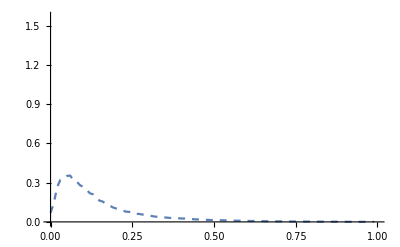

```mathematica
model4=f3[x]*b/a*Exp[-b*x];
fit4=FindFit[bounces[[4]],model4,{a,b},{x}]
f4=Function[{x},model4/.fit4];
Show[
ListLinePlot[bounces[[4]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[f4[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, « 18 »\ « 3 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.0644934}, {1/100, 0.166616}, {1/50, 0.279836}, {3/100, 0.419506}, {1/25, 0.443042}, {1/20, 0.478397}, {3/50, 0.502134}, {7/100, 0.494698}, {2/25, 0.491835}, {9/100, 0.483957}, {1/10, 0.488438}, {11/100, 0.470398}, {3/25, 0.459806}, « 26 », {39/100, 0.119022}, {2/5, 0.112911}, {41/100, 0.111181}, {21/50, 0.100149}, {43/100, 0.100375}, {11/25, 0.0907993}, {9/20, 0.0868527}, {23/50, 0.0823923}, {47/100, 0.0767546}, {12/25, 0.074217}, {49/100, 0.0700358}, « 50 »}, « 1 »/a, {a, « 4 »}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.0693927}, {1/100, 0.143651}, {1/50, 0.26385}, {3/100, 0.322373}, {1/25, 0.337571}, {1/20, 0.35135}, {3/50, 0.354244}, {7/100, 0.319268}, {2/25, 0.309136}, {9/100, 0.280834}, {1/10, 0.267669}, {11/100, 0.246085}, « 27 », {39/100, 0.0281648}, {2/5, 0.0260071}, {41/100, 0.025835}, {21/50, 0.0223387}, {43/100, 0.0223038}, {11/25, 0.0198382}, {9/20, 0.018868}, {23/50, 0.0175116}, {47/100, 0.0163779}, {12/25, 0.0157751}, {49/100, 0.0142339}, « 50 »}, 0.2\ « 1 » « 1 » (« 1 »)/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.0710948},{1/100,0.122751},{1/50,0.231749},{3/100,0.244973},{1/25,0.256463},{1/20,0.254999},{3/50,0.247028},{7/100,0.210107},{2/25,0.198163},{9/100,0.167491},{1/10,0.14918},{11/100,0.131886},{3/25,0.107224},{13/100,0.100223},{7/50,0.0818803},{3/20,0.0674053},{4/25,0.062132},{17/100,0.0521225},{9/50,0.0462889},{19/100,0.0392436},{1/5,0.0356969},{21/100,0.0313231},{11/50,0.0289066},{23/100,0.0243538},{6/25,0.0241502},{1/4,0.0226874},{13/50,0.0175204},{27/100,0.0180502},{7/25,0.0165147},{29/100,0.0156862},{3/10,0.0132858},{31/100,0.0122481},{8/25,0.0106309},{33/100,0.0102799},{17/50,0.00988922},{7/20,0.00882009},{9/25,0.00806535},{37/100,0.00752918},{19/50,0.00743939},{39/100,0.00707344},{2/5,0.00632301},{41/100,0.00650088},{21/50,0.00551134},{43/100,0.00545709},{11/25,0.00479412},{9/20,0.00458773},{23/50,0.00417904},{47/100,0.00387955},{12/25,0.00379824},{49/100,0.00329509},{1/2,0.00322222},{51/100,0.00322968},{13/25,0.00292598},{53/100,0.00287987},{27/50,0.00262959},{11/20,0.00236427},{14/25,0.00219033},{57/100,0.00210043},{29/50,0.00194661},{59/100,0.00163841},{3/5,0.00175601},{61/100,0.00157219},{31/50,0.00161902},{63/100,0.00140615},{16/25,0.00133573},{13/20,0.00124246},{33/50,0.00119598},{67/100,0.00107252},{17/25,0.00102929},{69/100,0.000985253},{7/10,0.000855737},{71/100,0.000823796},{18/25,0.000762064},{73/100,0.000708211},{37/50,0.00069264},{3/4,0.000613259},{19/25,0.000633219},{77/100,0.000539091},{39/50,0.000496603},{79/100,0.000486966},{4/5,0.000468542},{81/100,0.000429134},{41/50,0.000398785},{83/100,0.000378698},{21/25,0.000348031},{17/20,0.000338861},{43/50,0.000312764},{87/100,0.000274604},{22/25,0.000265275},{89/100,0.000232229},{9/10,0.000204292},{91/100,0.000176811},{23/25,0.000157403},{93/100,0.000130749},{47/50,0.000115549},{19/20,0.0000899288},{24/25,0.0000739003},{97/100,0.000053581},{49/50,0.0000363242},{99/100,0.0000148841}},1/a 0.2 ⅇ^(-0.2 x) (1/a 0.2 ⅇ^(-0.2 x) (1/a 0.2 ⅇ^(-0.2 x) ((2.1346 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.054395},{1/100,0.152475},{1/50,0.239881},{3/100,0.479152},{1/25,0.520947},{1/20,0.585763},{3/50,0.629567},{7/100,0.700074},{2/25,0.715666},{9/100,0.762299},{1/10,0.802291},{11/100,0.807603},{3/25,0.850698},{13/100,0.840319},{7/50,0.842531},{3/20,0.83661},{4/25,0.836818},{17/100,0.82575},{9/50,0.818634},{19/100,0.794592},{1/5,0.779717},{21/100,0.767559},{11/50,0.743065},{23/100,0.729495},{6/25,0.702015},{1/4,0.699104},{13/50,0.672219},{27/100,0.656018},{7/25,0.641828},{29/100,0.625966},{3/10,0.603964},{31/100,0.588366},{8/25,0.56578},{33/100,0.556027},{17/50,0.535956},{7/20,0.514761},{9/25,0.503237},{37/100,0.488762},{19/50,0.485569},{39/100,0.459003},{2/5,0.452825},{41/100,0.444365},{21/50,0.420585},{43/100,0.412303},{11/25,0.397904},{9/20,0.381721},{23/50,0.368878},{47/100,0.348123},{12/25,0.341466},{49/100,0.33173},{1/2,0.319601},{51/100,0.313889},{13/25,0.302581},{53/100,0.29237},{27/50,0.280077},{11/20,0.264326},{14/25,0.256872},{57/100,0.246509},{29/50,0.237268},{59/100,0.219962},{3/5,0.219278},{61/100,0.207675},{31/50,0.202776},{63/100,0.18844},{16/25,0.183443},{13/20,0.169733},{33/50,0.166748},{67/100,0.156425},{17/25,0.152156},{69/100,0.142797},{7/10,0.135249},{71/100,0.131059},{18/25,0.122857},{73/100,0.116432},{37/50,0.112112},{3/4,0.101487},{19/25,0.0999895},{77/100,0.0909519},{39/50,0.0867397},{79/100,0.0814425},{4/5,0.0763704},{81/100,0.0703441},{41/50,0.0662323},{83/100,0.060832},{21/25,0.056012},{17/20,0.0519434},{43/50,0.048115},{87/100,0.0434114},{22/25,0.0402554},{89/100,0.0354001},{9/10,0.0318146},{91/100,0.027814},{23/25,0.0243905},{93/100,0.0210489},{47/50,0.0182812},{19/20,0.0149027},{24/25,0.0120484},{97/100,0.00907089},{49/50,0.0061625},{99/100,0.00257255}},(2.1346 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}])/.FindFit[{{0,0.0644934},{1/100,0.166616},{1/50,0.279836},{3/100,0.419506},{1/25,0.443042},{1/20,0.478397},{3/50,0.502134},{7/100,0.494698},{2/25,0.491835},{9/100,0.483957},{1/10,0.488438},{11/100,0.470398},{3/25,0.459806},{13/100,0.44938},{7/50,0.417658},{3/20,0.395725},{4/25,0.388853},{17/100,0.360218},{9/50,0.345068},{19/100,0.320713},{1/5,0.301487},{21/100,0.29047},{11/50,0.275746},{23/100,0.255856},{6/25,0.24846},{1/4,0.239832},{13/50,0.216226},{27/100,0.2149},{7/25,0.202604},{29/100,0.192903},{3/10,0.180191},{31/100,0.172548},{8/25,0.160178},{33/100,0.156579},{17/50,0.148714},{7/20,0.137779},{9/25,0.132527},{37/100,0.126295},{19/50,0.124248},{39/100,0.119022},{2/5,0.112911},{41/100,0.111181},{21/50,0.100149},{43/100,0.100375},{11/25,0.0907993},{9/20,0.0868527},{23/50,0.0823923},{47/100,0.0767546},{12/25,0.074217},{49/100,0.0700358},{1/2,0.0681404},{51/100,0.0657395},{13/25,0.0619384},{53/100,0.0596653},{27/50,0.0561079},{11/20,0.0516134},{14/25,0.0494036},{57/100,0.0466142},{29/50,0.0447192},{59/100,0.0401356},{3/5,0.0398435},{61/100,0.0368706},{31/50,0.0365578},{63/100,0.0326591},{16/25,0.0320426},{13/20,0.0287873},{33/50,0.0279825},{67/100,0.0256719},{17/25,0.0247106},{69/100,0.0230628},{7/10,0.0214108},{71/100,0.0207132},{18/25,0.0189188},{73/100,0.0178012},{37/50,0.017209},{3/4,0.0150282},{19/25,0.0152946},{77/100,0.0135314},{39/50,0.0126362},{79/100,0.011726},{4/5,0.0110713},{81/100,0.0101247},{41/50,0.00952724},{83/100,0.00874461},{21/25,0.00802355},{17/20,0.00754802},{43/50,0.00695417},{87/100,0.00617516},{22/25,0.00580952},{89/100,0.00503901},{9/10,0.00449074},{91/100,0.00392841},{23/25,0.0034301},{93/100,0.00295668},{47/50,0.00259861},{19/20,0.00207451},{24/25,0.00169034},{97/100,0.00126655},{49/50,0.000861621},{99/100,0.000360172}},1/a 0.2 ⅇ^(-0.2 x) ((2.1346 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.054395},{1/100,0.152475},{1/50,0.239881},{3/100,0.479152},{1/25,0.520947},{1/20,0.585763},{3/50,0.629567},{7/100,0.700074},{2/25,0.715666},{9/100,0.762299},{1/10,0.802291},{11/100,0.807603},{3/25,0.850698},{13/100,0.840319},{7/50,0.842531},{3/20,0.83661},{4/25,0.836818},{17/100,0.82575},{9/50,0.818634},{19/100,0.794592},{1/5,0.779717},{21/100,0.767559},{11/50,0.743065},{23/100,0.729495},{6/25,0.702015},{1/4,0.699104},{13/50,0.672219},{27/100,0.656018},{7/25,0.641828},{29/100,0.625966},{3/10,0.603964},{31/100,0.588366},{8/25,0.56578},{33/100,0.556027},{17/50,0.535956},{7/20,0.514761},{9/25,0.503237},{37/100,0.488762},{19/50,0.485569},{39/100,0.459003},{2/5,0.452825},{41/100,0.444365},{21/50,0.420585},{43/100,0.412303},{11/25,0.397904},{9/20,0.381721},{23/50,0.368878},{47/100,0.348123},{12/25,0.341466},{49/100,0.33173},{1/2,0.319601},{51/100,0.313889},{13/25,0.302581},{53/100,0.29237},{27/50,0.280077},{11/20,0.264326},{14/25,0.256872},{57/100,0.246509},{29/50,0.237268},{59/100,0.219962},{3/5,0.219278},{61/100,0.207675},{31/50,0.202776},{63/100,0.18844},{16/25,0.183443},{13/20,0.169733},{33/50,0.166748},{67/100,0.156425},{17/25,0.152156},{69/100,0.142797},{7/10,0.135249},{71/100,0.131059},{18/25,0.122857},{73/100,0.116432},{37/50,0.112112},{3/4,0.101487},{19/25,0.0999895},{77/100,0.0909519},{39/50,0.0867397},{79/100,0.0814425},{4/5,0.0763704},{81/100,0.0703441},{41/50,0.0662323},{83/100,0.060832},{21/25,0.056012},{17/20,0.0519434},{43/50,0.048115},{87/100,0.0434114},{22/25,0.0402554},{89/100,0.0354001},{9/10,0.0318146},{91/100,0.027814},{23/25,0.0243905},{93/100,0.0210489},{47/50,0.0182812},{19/20,0.0149027},{24/25,0.0120484},{97/100,0.00907089},{49/50,0.0061625},{99/100,0.00257255}},(2.1346 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}]),{a,0.2},{x}])/.FindFit[{{0,0.0693927},{1/100,0.143651},{1/50,0.26385},{3/100,0.322373},{1/25,0.337571},{1/20,0.35135},{3/50,0.354244},{7/100,0.319268},{2/25,0.309136},{9/100,0.280834},{1/10,0.267669},{11/100,0.246085},{3/25,0.219542},{13/100,0.21063},{7/50,0.182554},{3/20,0.162658},{4/25,0.154918},{17/100,0.136437},{9/50,0.126039},{19/100,0.111606},{1/5,0.102752},{21/100,0.094796},{11/50,0.0883583},{23/100,0.0785198},{6/25,0.0767917},{1/4,0.0728438},{13/50,0.0605793},{27/100,0.0613124},{7/25,0.0566535},{29/100,0.0535274},{3/10,0.0480256},{31/100,0.0448069},{8/25,0.0401872},{33/100,0.039103},{17/50,0.0369998},{7/20,0.0337637},{9/25,0.031536},{37/100,0.0296872},{19/50,0.0292039},{39/100,0.0281648},{2/5,0.0260071},{41/100,0.025835},{21/50,0.0223387},{43/100,0.0223038},{11/25,0.0198382},{9/20,0.018868},{23/50,0.0175116},{47/100,0.0163779},{12/25,0.0157751},{49/100,0.0142339},{1/2,0.0139511},{51/100,0.0134869},{13/25,0.012514},{53/100,0.012168},{27/50,0.0112447},{11/20,0.0101705},{14/25,0.00962273},{57/100,0.00904694},{29/50,0.00857343},{59/100,0.00751649},{3/5,0.00758899},{61/100,0.0068866},{31/50,0.0070021},{63/100,0.00613189},{16/25,0.00596792},{13/20,0.0053878},{33/50,0.00520242},{67/100,0.00470617},{17/25,0.00454719},{69/100,0.00426061},{7/10,0.00383446},{71/100,0.00370982},{18/25,0.00339143},{73/100,0.00317931},{37/50,0.00308498},{3/4,0.00268804},{19/25,0.00278149},{77/100,0.00240284},{39/50,0.00222559},{79/100,0.00210539},{4/5,0.00201144},{81/100,0.00184267},{41/50,0.00172379},{83/100,0.00160137},{21/25,0.00147563},{17/20,0.00141124},{43/50,0.00129987},{87/100,0.00115179},{22/25,0.00109816},{89/100,0.000955549},{9/10,0.00084888},{91/100,0.00073853},{23/25,0.000650637},{93/100,0.000553029},{47/50,0.000489352},{19/20,0.000386077},{24/25,0.000316688},{97/100,0.000234163},{49/50,0.000159915},{99/100,0.0000665092}},1/a 0.2 ⅇ^(-0.2 x) (1/a 0.2 ⅇ^(-0.2 x) ((2.1346 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.054395},{1/100,0.152475},{1/50,0.239881},{3/100,0.479152},{1/25,0.520947},{1/20,0.585763},{3/50,0.629567},{7/100,0.700074},{2/25,0.715666},{9/100,0.762299},{1/10,0.802291},{11/100,0.807603},{3/25,0.850698},{13/100,0.840319},{7/50,0.842531},{3/20,0.83661},{4/25,0.836818},{17/100,0.82575},{9/50,0.818634},{19/100,0.794592},{1/5,0.779717},{21/100,0.767559},{11/50,0.743065},{23/100,0.729495},{6/25,0.702015},{1/4,0.699104},{13/50,0.672219},{27/100,0.656018},{7/25,0.641828},{29/100,0.625966},{3/10,0.603964},{31/100,0.588366},{8/25,0.56578},{33/100,0.556027},{17/50,0.535956},{7/20,0.514761},{9/25,0.503237},{37/100,0.488762},{19/50,0.485569},{39/100,0.459003},{2/5,0.452825},{41/100,0.444365},{21/50,0.420585},{43/100,0.412303},{11/25,0.397904},{9/20,0.381721},{23/50,0.368878},{47/100,0.348123},{12/25,0.341466},{49/100,0.33173},{1/2,0.319601},{51/100,0.313889},{13/25,0.302581},{53/100,0.29237},{27/50,0.280077},{11/20,0.264326},{14/25,0.256872},{57/100,0.246509},{29/50,0.237268},{59/100,0.219962},{3/5,0.219278},{61/100,0.207675},{31/50,0.202776},{63/100,0.18844},{16/25,0.183443},{13/20,0.169733},{33/50,0.166748},{67/100,0.156425},{17/25,0.152156},{69/100,0.142797},{7/10,0.135249},{71/100,0.131059},{18/25,0.122857},{73/100,0.116432},{37/50,0.112112},{3/4,0.101487},{19/25,0.0999895},{77/100,0.0909519},{39/50,0.0867397},{79/100,0.0814425},{4/5,0.0763704},{81/100,0.0703441},{41/50,0.0662323},{83/100,0.060832},{21/25,0.056012},{17/20,0.0519434},{43/50,0.048115},{87/100,0.0434114},{22/25,0.0402554},{89/100,0.0354001},{9/10,0.0318146},{91/100,0.027814},{23/25,0.0243905},{93/100,0.0210489},{47/50,0.0182812},{19/20,0.0149027},{24/25,0.0120484},{97/100,0.00907089},{49/50,0.0061625},{99/100,0.00257255}},(2.1346 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}])/.FindFit[{{0,0.0644934},{1/100,0.166616},{1/50,0.279836},{3/100,0.419506},{1/25,0.443042},{1/20,0.478397},{3/50,0.502134},{7/100,0.494698},{2/25,0.491835},{9/100,0.483957},{1/10,0.488438},{11/100,0.470398},{3/25,0.459806},{13/100,0.44938},{7/50,0.417658},{3/20,0.395725},{4/25,0.388853},{17/100,0.360218},{9/50,0.345068},{19/100,0.320713},{1/5,0.301487},{21/100,0.29047},{11/50,0.275746},{23/100,0.255856},{6/25,0.24846},{1/4,0.239832},{13/50,0.216226},{27/100,0.2149},{7/25,0.202604},{29/100,0.192903},{3/10,0.180191},{31/100,0.172548},{8/25,0.160178},{33/100,0.156579},{17/50,0.148714},{7/20,0.137779},{9/25,0.132527},{37/100,0.126295},{19/50,0.124248},{39/100,0.119022},{2/5,0.112911},{41/100,0.111181},{21/50,0.100149},{43/100,0.100375},{11/25,0.0907993},{9/20,0.0868527},{23/50,0.0823923},{47/100,0.0767546},{12/25,0.074217},{49/100,0.0700358},{1/2,0.0681404},{51/100,0.0657395},{13/25,0.0619384},{53/100,0.0596653},{27/50,0.0561079},{11/20,0.0516134},{14/25,0.0494036},{57/100,0.0466142},{29/50,0.0447192},{59/100,0.0401356},{3/5,0.0398435},{61/100,0.0368706},{31/50,0.0365578},{63/100,0.0326591},{16/25,0.0320426},{13/20,0.0287873},{33/50,0.0279825},{67/100,0.0256719},{17/25,0.0247106},{69/100,0.0230628},{7/10,0.0214108},{71/100,0.0207132},{18/25,0.0189188},{73/100,0.0178012},{37/50,0.017209},{3/4,0.0150282},{19/25,0.0152946},{77/100,0.0135314},{39/50,0.0126362},{79/100,0.011726},{4/5,0.0110713},{81/100,0.0101247},{41/50,0.00952724},{83/100,0.00874461},{21/25,0.00802355},{17/20,0.00754802},{43/50,0.00695417},{87/100,0.00617516},{22/25,0.00580952},{89/100,0.00503901},{9/10,0.00449074},{91/100,0.00392841},{23/25,0.0034301},{93/100,0.00295668},{47/50,0.00259861},{19/20,0.00207451},{24/25,0.00169034},{97/100,0.00126655},{49/50,0.000861621},{99/100,0.000360172}},1/a 0.2 ⅇ^(-0.2 x) ((2.1346 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.054395},{1/100,0.152475},{1/50,0.239881},{3/100,0.479152},{1/25,0.520947},{1/20,0.585763},{3/50,0.629567},{7/100,0.700074},{2/25,0.715666},{9/100,0.762299},{1/10,0.802291},{11/100,0.807603},{3/25,0.850698},{13/100,0.840319},{7/50,0.842531},{3/20,0.83661},{4/25,0.836818},{17/100,0.82575},{9/50,0.818634},{19/100,0.794592},{1/5,0.779717},{21/100,0.767559},{11/50,0.743065},{23/100,0.729495},{6/25,0.702015},{1/4,0.699104},{13/50,0.672219},{27/100,0.656018},{7/25,0.641828},{29/100,0.625966},{3/10,0.603964},{31/100,0.588366},{8/25,0.56578},{33/100,0.556027},{17/50,0.535956},{7/20,0.514761},{9/25,0.503237},{37/100,0.488762},{19/50,0.485569},{39/100,0.459003},{2/5,0.452825},{41/100,0.444365},{21/50,0.420585},{43/100,0.412303},{11/25,0.397904},{9/20,0.381721},{23/50,0.368878},{47/100,0.348123},{12/25,0.341466},{49/100,0.33173},{1/2,0.319601},{51/100,0.313889},{13/25,0.302581},{53/100,0.29237},{27/50,0.280077},{11/20,0.264326},{14/25,0.256872},{57/100,0.246509},{29/50,0.237268},{59/100,0.219962},{3/5,0.219278},{61/100,0.207675},{31/50,0.202776},{63/100,0.18844},{16/25,0.183443},{13/20,0.169733},{33/50,0.166748},{67/100,0.156425},{17/25,0.152156},{69/100,0.142797},{7/10,0.135249},{71/100,0.131059},{18/25,0.122857},{73/100,0.116432},{37/50,0.112112},{3/4,0.101487},{19/25,0.0999895},{77/100,0.0909519},{39/50,0.0867397},{79/100,0.0814425},{4/5,0.0763704},{81/100,0.0703441},{41/50,0.0662323},{83/100,0.060832},{21/25,0.056012},{17/20,0.0519434},{43/50,0.048115},{87/100,0.0434114},{22/25,0.0402554},{89/100,0.0354001},{9/10,0.0318146},{91/100,0.027814},{23/25,0.0243905},{93/100,0.0210489},{47/50,0.0182812},{19/20,0.0149027},{24/25,0.0120484},{97/100,0.00907089},{49/50,0.0061625},{99/100,0.00257255}},(2.1346 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}]),{a,0.2},{x}]),{a,0.2},{x}]),{a,0.2},{x}]

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, « 3 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, « 3 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.0644934}, {1/100, 0.166616}, {1/50, 0.279836}, {3/100, 0.419506}, {1/25, 0.443042}, {1/20, 0.478397}, {3/50, 0.502134}, {7/100, 0.494698}, {2/25, 0.491835}, {9/100, 0.483957}, {1/10, 0.488438}, {11/100, 0.470398}, {3/25, 0.459806}, « 26 », {39/100, 0.119022}, {2/5, 0.112911}, {41/100, 0.111181}, {21/50, 0.100149}, {43/100, 0.100375}, {11/25, 0.0907993}, {9/20, 0.0868527}, {23/50, 0.0823923}, {47/100, 0.0767546}, {12/25, 0.074217}, {49/100, 0.0700358}, « 50 »}, « 1 »/a, « 1 », {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

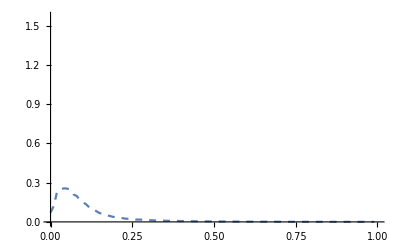

```mathematica
model5=f4[x]*b/a*Exp[-b*x];
fit5=FindFit[bounces[[5]],model5,{a,b},{x}]
f5=Function[{x},model5/.fit5];
Show[
ListLinePlot[bounces[[5]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[f5[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.0370465},{1/100,0.101578},{1/50,0.140295},{3/100,0.331004},{1/25,0.430845},{1/20,0.487528},{3/50,0.530333},{7/100,0.661051},{2/25,0.708549},{9/100,0.831567},{1/10,0.883113},{11/100,0.950927},{3/25,1.01651},{13/100,1.04012},{7/50,1.11703},{3/20,1.17885},{4/25,1.17571},{17/100,1.22822},{9/50,1.24314},{19/100,1.28731},{1/5,1.30311},{21/100,1.3138},{11/50,1.33189},{23/100,1.35278},{6/25,1.35708},{1/4,1.34283},{13/50,1.38242},{27/100,1.36702},{7/25,1.36835},{29/100,1.36541},{3/10,1.37978},{31/100,1.37553},{8/25,1.3856},{33/100,1.36891},{17/50,1.36709},{7/20,1.3731},{9/25,1.36113},{37/100,1.3528},{19/50,1.32694},{39/100,1.32892},{2/5,1.31262},{41/100,1.29091},{21/50,1.29836},{43/100,1.2747},{11/25,1.27036},{9/20,1.2603},{23/50,1.24748},{47/100,1.2435},{12/25,1.22193},{49/100,1.2061},{1/2,1.18878},{51/100,1.16557},{13/25,1.15017},{53/100,1.13102},{27/50,1.11675},{11/20,1.10669},{14/25,1.08536},{57/100,1.06771},{29/50,1.04719},{59/100,1.03948},{3/5,1.00789},{61/100,0.991967},{31/50,0.964771},{63/100,0.952481},{16/25,0.927581},{13/20,0.91287},{33/50,0.885056},{67/100,0.866522},{17/25,0.840205},{69/100,0.819874},{7/10,0.797931},{71/100,0.771952},{18/25,0.749985},{73/100,0.726102},{37/50,0.699958},{3/4,0.680613},{19/25,0.650514},{77/100,0.629736},{39/50,0.603668},{79/100,0.578258},{4/5,0.552745},{81/100,0.527912},{41/50,0.500997},{83/100,0.475437},{21/25,0.449504},{17/20,0.422701},{43/50,0.395322},{87/100,0.369072},{22/25,0.341089},{89/100,0.315506},{9/10,0.288208},{91/100,0.260755},{23/25,0.233527},{93/100,0.205472},{47/50,0.177028},{19/20,0.14957},{24/25,0.120909},{97/100,0.0933104},{49/50,0.0650488},{99/100,0.0282958}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}]

ReplaceAll::reps: {FindFit[{{0, 0.0370465}, {1/100, 0.101578}, {1/50, 0.140295}, {3/100, 0.331004}, {1/25, 0.430845}, {1/20, 0.487528}, {3/50, 0.530333}, {7/100, 0.661051}, {2/25, 0.708549}, {9/100, 0.831567}, {1/10, 0.883113}, {11/100, 0.950927}, {3/25, 1.01651}, « 25 », {19/50, 1.32694}, {39/100, 1.32892}, {2/5, 1.31262}, {41/100, 1.29091}, {21/50, 1.29836}, {43/100, 1.2747}, {11/25, 1.27036}, {9/20, 1.2603}, {23/50, 1.24748}, {47/100, 1.2435}, {12/25, 1.22193}, {49/100, 1.2061}, « 50 »}, « 2 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0., 0.0370465}, {0.01, 0.101578}, {0.02, 0.140295}, {0.03, 0.331004}, {0.04, 0.430845}, {0.05, 0.487528}, {0.06, 0.530333}, {0.07, 0.661051}, {0.08, 0.708549}, {0.09, 0.831567}, {0.1, 0.883113}, {0.11, 0.950927}, « 27 », {0.39, 1.32892}, {0.4, 1.31262}, {0.41, 1.29091}, {0.42, 1.29836}, {0.43, 1.2747}, {0.44, 1.27036}, {0.45, 1.2603}, {0.46, 1.24748}, {0.47, 1.2435}, {0.48, 1.22193}, {0.49, 1.2061}, « 50 »}, « 1 », « 1 », {0.0000204286}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

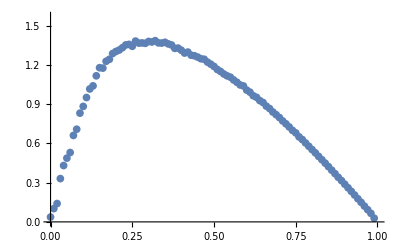

```mathematica
modelFit1=FindFit[bounces[[1]], model,{a,b},{x}]
bounce1=Function[{x},Evaluate[model/.modelFit1]];
Show[
ListPlot[bounces[[1]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce1[x],{x,0,1},PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.054395},{1/100,0.152475},{1/50,0.239881},{3/100,0.479152},{1/25,0.520947},{1/20,0.585763},{3/50,0.629567},{7/100,0.700074},{2/25,0.715666},{9/100,0.762299},{1/10,0.802291},{11/100,0.807603},{3/25,0.850698},{13/100,0.840319},{7/50,0.842531},{3/20,0.83661},{4/25,0.836818},{17/100,0.82575},{9/50,0.818634},{19/100,0.794592},{1/5,0.779717},{21/100,0.767559},{11/50,0.743065},{23/100,0.729495},{6/25,0.702015},{1/4,0.699104},{13/50,0.672219},{27/100,0.656018},{7/25,0.641828},{29/100,0.625966},{3/10,0.603964},{31/100,0.588366},{8/25,0.56578},{33/100,0.556027},{17/50,0.535956},{7/20,0.514761},{9/25,0.503237},{37/100,0.488762},{19/50,0.485569},{39/100,0.459003},{2/5,0.452825},{41/100,0.444365},{21/50,0.420585},{43/100,0.412303},{11/25,0.397904},{9/20,0.381721},{23/50,0.368878},{47/100,0.348123},{12/25,0.341466},{49/100,0.33173},{1/2,0.319601},{51/100,0.313889},{13/25,0.302581},{53/100,0.29237},{27/50,0.280077},{11/20,0.264326},{14/25,0.256872},{57/100,0.246509},{29/50,0.237268},{59/100,0.219962},{3/5,0.219278},{61/100,0.207675},{31/50,0.202776},{63/100,0.18844},{16/25,0.183443},{13/20,0.169733},{33/50,0.166748},{67/100,0.156425},{17/25,0.152156},{69/100,0.142797},{7/10,0.135249},{71/100,0.131059},{18/25,0.122857},{73/100,0.116432},{37/50,0.112112},{3/4,0.101487},{19/25,0.0999895},{77/100,0.0909519},{39/50,0.0867397},{79/100,0.0814425},{4/5,0.0763704},{81/100,0.0703441},{41/50,0.0662323},{83/100,0.060832},{21/25,0.056012},{17/20,0.0519434},{43/50,0.048115},{87/100,0.0434114},{22/25,0.0402554},{89/100,0.0354001},{9/10,0.0318146},{91/100,0.027814},{23/25,0.0243905},{93/100,0.0210489},{47/50,0.0182812},{19/20,0.0149027},{24/25,0.0120484},{97/100,0.00907089},{49/50,0.0061625},{99/100,0.00257255}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}]

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, 0.2\ « 3 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, « 3 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0., 0.054395}, {0.01, 0.152475}, {0.02, 0.239881}, {0.03, 0.479152}, {0.04, 0.520947}, {0.05, 0.585763}, {0.06, 0.629567}, {0.07, 0.700074}, {0.08, 0.715666}, {0.09, 0.762299}, {0.1, 0.802291}, {0.11, 0.807603}, « 27 », {0.39, 0.459003}, {0.4, 0.452825}, {0.41, 0.444365}, {0.42, 0.420585}, {0.43, 0.412303}, {0.44, 0.397904}, {0.45, 0.381721}, {0.46, 0.368878}, {0.47, 0.348123}, {0.48, 0.341466}, {0.49, 0.33173}, « 50 »}, « 2 », {0.0000204286}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

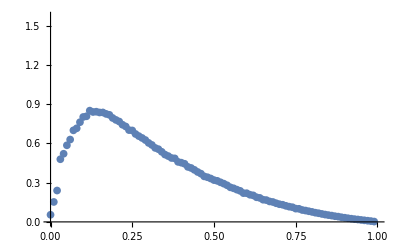

```mathematica
modelFit2=FindFit[bounces[[2]], model,{a,b},{x}]
bounce2=Function[{x},Evaluate[model/.modelFit2]];
Show[
ListPlot[bounces[[2]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce2[x],{x,0,1},PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.0644934},{1/100,0.166616},{1/50,0.279836},{3/100,0.419506},{1/25,0.443042},{1/20,0.478397},{3/50,0.502134},{7/100,0.494698},{2/25,0.491835},{9/100,0.483957},{1/10,0.488438},{11/100,0.470398},{3/25,0.459806},{13/100,0.44938},{7/50,0.417658},{3/20,0.395725},{4/25,0.388853},{17/100,0.360218},{9/50,0.345068},{19/100,0.320713},{1/5,0.301487},{21/100,0.29047},{11/50,0.275746},{23/100,0.255856},{6/25,0.24846},{1/4,0.239832},{13/50,0.216226},{27/100,0.2149},{7/25,0.202604},{29/100,0.192903},{3/10,0.180191},{31/100,0.172548},{8/25,0.160178},{33/100,0.156579},{17/50,0.148714},{7/20,0.137779},{9/25,0.132527},{37/100,0.126295},{19/50,0.124248},{39/100,0.119022},{2/5,0.112911},{41/100,0.111181},{21/50,0.100149},{43/100,0.100375},{11/25,0.0907993},{9/20,0.0868527},{23/50,0.0823923},{47/100,0.0767546},{12/25,0.074217},{49/100,0.0700358},{1/2,0.0681404},{51/100,0.0657395},{13/25,0.0619384},{53/100,0.0596653},{27/50,0.0561079},{11/20,0.0516134},{14/25,0.0494036},{57/100,0.0466142},{29/50,0.0447192},{59/100,0.0401356},{3/5,0.0398435},{61/100,0.0368706},{31/50,0.0365578},{63/100,0.0326591},{16/25,0.0320426},{13/20,0.0287873},{33/50,0.0279825},{67/100,0.0256719},{17/25,0.0247106},{69/100,0.0230628},{7/10,0.0214108},{71/100,0.0207132},{18/25,0.0189188},{73/100,0.0178012},{37/50,0.017209},{3/4,0.0150282},{19/25,0.0152946},{77/100,0.0135314},{39/50,0.0126362},{79/100,0.011726},{4/5,0.0110713},{81/100,0.0101247},{41/50,0.00952724},{83/100,0.00874461},{21/25,0.00802355},{17/20,0.00754802},{43/50,0.00695417},{87/100,0.00617516},{22/25,0.00580952},{89/100,0.00503901},{9/10,0.00449074},{91/100,0.00392841},{23/25,0.0034301},{93/100,0.00295668},{47/50,0.00259861},{19/20,0.00207451},{24/25,0.00169034},{97/100,0.00126655},{49/50,0.000861621},{99/100,0.000360172}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}]

ReplaceAll::reps: {FindFit[{{0, 0.0644934}, {1/100, 0.166616}, {1/50, 0.279836}, {3/100, 0.419506}, {1/25, 0.443042}, {1/20, 0.478397}, {3/50, 0.502134}, {7/100, 0.494698}, {2/25, 0.491835}, {9/100, 0.483957}, {1/10, 0.488438}, {11/100, 0.470398}, {3/25, 0.459806}, « 26 », {39/100, 0.119022}, {2/5, 0.112911}, {41/100, 0.111181}, {21/50, 0.100149}, {43/100, 0.100375}, {11/25, 0.0907993}, {9/20, 0.0868527}, {23/50, 0.0823923}, {47/100, 0.0767546}, {12/25, 0.074217}, {49/100, 0.0700358}, « 50 »}, « 1 »/a, {a, « 4 »}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.0644934}, {1/100, 0.166616}, {1/50, 0.279836}, {3/100, 0.419506}, {1/25, 0.443042}, {1/20, 0.478397}, {3/50, 0.502134}, {7/100, 0.494698}, {2/25, 0.491835}, {9/100, 0.483957}, {1/10, 0.488438}, {11/100, 0.470398}, {3/25, 0.459806}, « 26 », {39/100, 0.119022}, {2/5, 0.112911}, {41/100, 0.111181}, {21/50, 0.100149}, {43/100, 0.100375}, {11/25, 0.0907993}, {9/20, 0.0868527}, {23/50, 0.0823923}, {47/100, 0.0767546}, {12/25, 0.074217}, {49/100, 0.0700358}, « 50 »}, « 22 »/a, {« 1 »}, {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0., 0.0644934}, {0.01, 0.166616}, {0.02, 0.279836}, {0.03, 0.419506}, {0.04, 0.443042}, {0.05, 0.478397}, {0.06, 0.502134}, {0.07, 0.494698}, {0.08, 0.491835}, {0.09, 0.483957}, {0.1, 0.488438}, {0.11, 0.470398}, « 27 », {0.39, 0.119022}, {0.4, 0.112911}, {0.41, 0.111181}, {0.42, 0.100149}, {0.43, 0.100375}, {0.44, 0.0907993}, {0.45, 0.0868527}, {0.46, 0.0823923}, {0.47, 0.0767546}, {0.48, 0.074217}, {0.49, 0.0700358}, « 50 »}, « 22 »/a, « 1 », {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.0644934}, {1/100, 0.166616}, {1/50, 0.279836}, {3/100, 0.419506}, {1/25, 0.443042}, {1/20, 0.478397}, {3/50, 0.502134}, {7/100, 0.494698}, {2/25, 0.491835}, {9/100, 0.483957}, {1/10, 0.488438}, {11/100, 0.470398}, {3/25, 0.459806}, « 26 », {39/100, 0.119022}, {2/5, 0.112911}, {41/100, 0.111181}, {21/50, 0.100149}, {43/100, 0.100375}, {11/25, 0.0907993}, {9/20, 0.0868527}, {23/50, 0.0823923}, {47/100, 0.0767546}, {12/25, 0.074217}, {49/100, 0.0700358}, « 50 »}, « 22 »/a, {« 1 »}, {« 20 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

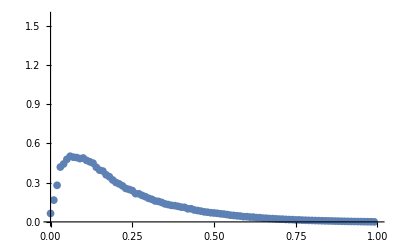

```mathematica
modelFit3=FindFit[bounces[[3]], model,{a,b},{x}]
bounce3=Function[{x},Evaluate[model/.modelFit3]];
Show[
ListPlot[bounces[[3]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce3[x],{x,0,1},PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.0693927},{1/100,0.143651},{1/50,0.26385},{3/100,0.322373},{1/25,0.337571},{1/20,0.35135},{3/50,0.354244},{7/100,0.319268},{2/25,0.309136},{9/100,0.280834},{1/10,0.267669},{11/100,0.246085},{3/25,0.219542},{13/100,0.21063},{7/50,0.182554},{3/20,0.162658},{4/25,0.154918},{17/100,0.136437},{9/50,0.126039},{19/100,0.111606},{1/5,0.102752},{21/100,0.094796},{11/50,0.0883583},{23/100,0.0785198},{6/25,0.0767917},{1/4,0.0728438},{13/50,0.0605793},{27/100,0.0613124},{7/25,0.0566535},{29/100,0.0535274},{3/10,0.0480256},{31/100,0.0448069},{8/25,0.0401872},{33/100,0.039103},{17/50,0.0369998},{7/20,0.0337637},{9/25,0.031536},{37/100,0.0296872},{19/50,0.0292039},{39/100,0.0281648},{2/5,0.0260071},{41/100,0.025835},{21/50,0.0223387},{43/100,0.0223038},{11/25,0.0198382},{9/20,0.018868},{23/50,0.0175116},{47/100,0.0163779},{12/25,0.0157751},{49/100,0.0142339},{1/2,0.0139511},{51/100,0.0134869},{13/25,0.012514},{53/100,0.012168},{27/50,0.0112447},{11/20,0.0101705},{14/25,0.00962273},{57/100,0.00904694},{29/50,0.00857343},{59/100,0.00751649},{3/5,0.00758899},{61/100,0.0068866},{31/50,0.0070021},{63/100,0.00613189},{16/25,0.00596792},{13/20,0.0053878},{33/50,0.00520242},{67/100,0.00470617},{17/25,0.00454719},{69/100,0.00426061},{7/10,0.00383446},{71/100,0.00370982},{18/25,0.00339143},{73/100,0.00317931},{37/50,0.00308498},{3/4,0.00268804},{19/25,0.00278149},{77/100,0.00240284},{39/50,0.00222559},{79/100,0.00210539},{4/5,0.00201144},{81/100,0.00184267},{41/50,0.00172379},{83/100,0.00160137},{21/25,0.00147563},{17/20,0.00141124},{43/50,0.00129987},{87/100,0.00115179},{22/25,0.00109816},{89/100,0.000955549},{9/10,0.00084888},{91/100,0.00073853},{23/25,0.000650637},{93/100,0.000553029},{47/50,0.000489352},{19/20,0.000386077},{24/25,0.000316688},{97/100,0.000234163},{49/50,0.000159915},{99/100,0.0000665092}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}]

ReplaceAll::reps: {FindFit[{{0, 0.0693927}, {1/100, 0.143651}, {1/50, 0.26385}, {3/100, 0.322373}, {1/25, 0.337571}, {1/20, 0.35135}, {3/50, 0.354244}, {7/100, 0.319268}, {2/25, 0.309136}, {9/100, 0.280834}, {1/10, 0.267669}, {11/100, 0.246085}, « 27 », {39/100, 0.0281648}, {2/5, 0.0260071}, {41/100, 0.025835}, {21/50, 0.0223387}, {43/100, 0.0223038}, {11/25, 0.0198382}, {9/20, 0.018868}, {23/50, 0.0175116}, {47/100, 0.0163779}, {12/25, 0.0157751}, {49/100, 0.0142339}, « 50 »}, 0.2\ « 1 » « 1 » « 1 »\ x/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.0693927}, {1/100, 0.143651}, {1/50, 0.26385}, {3/100, 0.322373}, {1/25, 0.337571}, {1/20, 0.35135}, {3/50, 0.354244}, {7/100, 0.319268}, {2/25, 0.309136}, {9/100, 0.280834}, {1/10, 0.267669}, {11/100, 0.246085}, « 27 », {39/100, 0.0281648}, {2/5, 0.0260071}, {41/100, 0.025835}, {21/50, 0.0223387}, {43/100, 0.0223038}, {11/25, 0.0198382}, {9/20, 0.018868}, {23/50, 0.0175116}, {47/100, 0.0163779}, {12/25, 0.0157751}, {49/100, 0.0142339}, « 50 »}, « 22 »/a, « 1 », {0.0000204286}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.0693927}, {1/100, 0.143651}, {1/50, 0.26385}, {3/100, 0.322373}, {1/25, 0.337571}, {1/20, 0.35135}, {3/50, 0.354244}, {7/100, 0.319268}, {2/25, 0.309136}, {9/100, 0.280834}, {1/10, 0.267669}, {11/100, 0.246085}, « 27 », {39/100, 0.0281648}, {2/5, 0.0260071}, {41/100, 0.025835}, {21/50, 0.0223387}, {43/100, 0.0223038}, {11/25, 0.0198382}, {9/20, 0.018868}, {23/50, 0.0175116}, {47/100, 0.0163779}, {12/25, 0.0157751}, {49/100, 0.0142339}, « 50 »}, « 22 »/a, {a, « 4 »}, {0.0204286}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

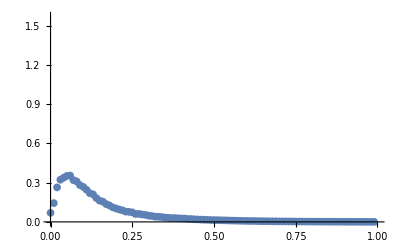

```mathematica
modelFit4=FindFit[bounces[[4]], model,{a,b},{x}]
bounce4=Function[{x},Evaluate[model/.modelFit4]];
Show[
ListPlot[bounces[[4]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce4[x],{x,0,1},PlotStyle->Red]
]
```

```mathematica
coeffsA={a/.modelFit1,a/.modelFit2,a/.modelFit3,a/.modelFit4}
coeffsB={b/.modelFit1,b/.modelFit2,b/.modelFit3,b/.modelFit4}
ListPlot[coeffsA]
ListPlot[coeffsB]
```

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.0370465}, {1/100, 0.101578}, {1/50, 0.140295}, {3/100, 0.331004}, {1/25, 0.430845}, {1/20, 0.487528}, {3/50, 0.530333}, {7/100, 0.661051}, {2/25, 0.708549}, {9/100, 0.831567}, {1/10, 0.883113}, {11/100, 0.950927}, {3/25, 1.01651}, « 25 », {19/50, 1.32694}, {39/100, 1.32892}, {2/5, 1.31262}, {41/100, 1.29091}, {21/50, 1.29836}, {43/100, 1.2747}, {11/25, 1.27036}, {9/20, 1.2603}, {23/50, 1.24748}, {47/100, 1.2435}, {12/25, 1.22193}, {49/100, 1.2061}, « 50 »}, « 2 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, 0.2\ « 3 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.0644934}, {1/100, 0.166616}, {1/50, 0.279836}, {3/100, 0.419506}, {1/25, 0.443042}, {1/20, 0.478397}, {3/50, 0.502134}, {7/100, 0.494698}, {2/25, 0.491835}, {9/100, 0.483957}, {1/10, 0.488438}, {11/100, 0.470398}, {3/25, 0.459806}, « 26 », {39/100, 0.119022}, {2/5, 0.112911}, {41/100, 0.111181}, {21/50, 0.100149}, {43/100, 0.100375}, {11/25, 0.0907993}, {9/20, 0.0868527}, {23/50, 0.0823923}, {47/100, 0.0767546}, {12/25, 0.074217}, {49/100, 0.0700358}, « 50 »}, « 1 »/a, {a, « 4 »}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{a/.FindFit[{{0,0.0370465},{1/100,0.101578},{1/50,0.140295},{3/100,0.331004},{1/25,0.430845},{1/20,0.487528},{3/50,0.530333},{7/100,0.661051},{2/25,0.708549},{9/100,0.831567},{1/10,0.883113},{11/100,0.950927},{3/25,1.01651},{13/100,1.04012},{7/50,1.11703},{3/20,1.17885},{4/25,1.17571},{17/100,1.22822},{9/50,1.24314},{19/100,1.28731},{1/5,1.30311},{21/100,1.3138},{11/50,1.33189},{23/100,1.35278},{6/25,1.35708},{1/4,1.34283},{13/50,1.38242},{27/100,1.36702},{7/25,1.36835},{29/100,1.36541},{3/10,1.37978},{31/100,1.37553},{8/25,1.3856},{33/100,1.36891},{17/50,1.36709},{7/20,1.3731},{9/25,1.36113},{37/100,1.3528},{19/50,1.32694},{39/100,1.32892},{2/5,1.31262},{41/100,1.29091},{21/50,1.29836},{43/100,1.2747},{11/25,1.27036},{9/20,1.2603},{23/50,1.24748},{47/100,1.2435},{12/25,1.22193},{49/100,1.2061},{1/2,1.18878},{51/100,1.16557},{13/25,1.15017},{53/100,1.13102},{27/50,1.11675},{11/20,1.10669},{14/25,1.08536},{57/100,1.06771},{29/50,1.04719},{59/100,1.03948},{3/5,1.00789},{61/100,0.991967},{31/50,0.964771},{63/100,0.952481},{16/25,0.927581},{13/20,0.91287},{33/50,0.885056},{67/100,0.866522},{17/25,0.840205},{69/100,0.819874},{7/10,0.797931},{71/100,0.771952},{18/25,0.749985},{73/100,0.726102},{37/50,0.699958},{3/4,0.680613},{19/25,0.650514},{77/100,0.629736},{39/50,0.603668},{79/100,0.578258},{4/5,0.552745},{81/100,0.527912},{41/50,0.500997},{83/100,0.475437},{21/25,0.449504},{17/20,0.422701},{43/50,0.395322},{87/100,0.369072},{22/25,0.341089},{89/100,0.315506},{9/10,0.288208},{91/100,0.260755},{23/25,0.233527},{93/100,0.205472},{47/50,0.177028},{19/20,0.14957},{24/25,0.120909},{97/100,0.0933104},{49/50,0.0650488},{99/100,0.0282958}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}],a/.FindFit[{{0,0.054395},{1/100,0.152475},{1/50,0.239881},{3/100,0.479152},{1/25,0.520947},{1/20,0.585763},{3/50,0.629567},{7/100,0.700074},{2/25,0.715666},{9/100,0.762299},{1/10,0.802291},{11/100,0.807603},{3/25,0.850698},{13/100,0.840319},{7/50,0.842531},{3/20,0.83661},{4/25,0.836818},{17/100,0.82575},{9/50,0.818634},{19/100,0.794592},{1/5,0.779717},{21/100,0.767559},{11/50,0.743065},{23/100,0.729495},{6/25,0.702015},{1/4,0.699104},{13/50,0.672219},{27/100,0.656018},{7/25,0.641828},{29/100,0.625966},{3/10,0.603964},{31/100,0.588366},{8/25,0.56578},{33/100,0.556027},{17/50,0.535956},{7/20,0.514761},{9/25,0.503237},{37/100,0.488762},{19/50,0.485569},{39/100,0.459003},{2/5,0.452825},{41/100,0.444365},{21/50,0.420585},{43/100,0.412303},{11/25,0.397904},{9/20,0.381721},{23/50,0.368878},{47/100,0.348123},{12/25,0.341466},{49/100,0.33173},{1/2,0.319601},{51/100,0.313889},{13/25,0.302581},{53/100,0.29237},{27/50,0.280077},{11/20,0.264326},{14/25,0.256872},{57/100,0.246509},{29/50,0.237268},{59/100,0.219962},{3/5,0.219278},{61/100,0.207675},{31/50,0.202776},{63/100,0.18844},{16/25,0.183443},{13/20,0.169733},{33/50,0.166748},{67/100,0.156425},{17/25,0.152156},{69/100,0.142797},{7/10,0.135249},{71/100,0.131059},{18/25,0.122857},{73/100,0.116432},{37/50,0.112112},{3/4,0.101487},{19/25,0.0999895},{77/100,0.0909519},{39/50,0.0867397},{79/100,0.0814425},{4/5,0.0763704},{81/100,0.0703441},{41/50,0.0662323},{83/100,0.060832},{21/25,0.056012},{17/20,0.0519434},{43/50,0.048115},{87/100,0.0434114},{22/25,0.0402554},{89/100,0.0354001},{9/10,0.0318146},{91/100,0.027814},{23/25,0.0243905},{93/100,0.0210489},{47/50,0.0182812},{19/20,0.0149027},{24/25,0.0120484},{97/100,0.00907089},{49/50,0.0061625},{99/100,0.00257255}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}],a/.FindFit[{{0,0.0644934},{1/100,0.166616},{1/50,0.279836},{3/100,0.419506},{1/25,0.443042},{1/20,0.478397},{3/50,0.502134},{7/100,0.494698},{2/25,0.491835},{9/100,0.483957},{1/10,0.488438},{11/100,0.470398},{3/25,0.459806},{13/100,0.44938},{7/50,0.417658},{3/20,0.395725},{4/25,0.388853},{17/100,0.360218},{9/50,0.345068},{19/100,0.320713},{1/5,0.301487},{21/100,0.29047},{11/50,0.275746},{23/100,0.255856},{6/25,0.24846},{1/4,0.239832},{13/50,0.216226},{27/100,0.2149},{7/25,0.202604},{29/100,0.192903},{3/10,0.180191},{31/100,0.172548},{8/25,0.160178},{33/100,0.156579},{17/50,0.148714},{7/20,0.137779},{9/25,0.132527},{37/100,0.126295},{19/50,0.124248},{39/100,0.119022},{2/5,0.112911},{41/100,0.111181},{21/50,0.100149},{43/100,0.100375},{11/25,0.0907993},{9/20,0.0868527},{23/50,0.0823923},{47/100,0.0767546},{12/25,0.074217},{49/100,0.0700358},{1/2,0.0681404},{51/100,0.0657395},{13/25,0.0619384},{53/100,0.0596653},{27/50,0.0561079},{11/20,0.0516134},{14/25,0.0494036},{57/100,0.0466142},{29/50,0.0447192},{59/100,0.0401356},{3/5,0.0398435},{61/100,0.0368706},{31/50,0.0365578},{63/100,0.0326591},{16/25,0.0320426},{13/20,0.0287873},{33/50,0.0279825},{67/100,0.0256719},{17/25,0.0247106},{69/100,0.0230628},{7/10,0.0214108},{71/100,0.0207132},{18/25,0.0189188},{73/100,0.0178012},{37/50,0.017209},{3/4,0.0150282},{19/25,0.0152946},{77/100,0.0135314},{39/50,0.0126362},{79/100,0.011726},{4/5,0.0110713},{81/100,0.0101247},{41/50,0.00952724},{83/100,0.00874461},{21/25,0.00802355},{17/20,0.00754802},{43/50,0.00695417},{87/100,0.00617516},{22/25,0.00580952},{89/100,0.00503901},{9/10,0.00449074},{91/100,0.00392841},{23/25,0.0034301},{93/100,0.00295668},{47/50,0.00259861},{19/20,0.00207451},{24/25,0.00169034},{97/100,0.00126655},{49/50,0.000861621},{99/100,0.000360172}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}],a/.FindFit[{{0,0.0693927},{1/100,0.143651},{1/50,0.26385},{3/100,0.322373},{1/25,0.337571},{1/20,0.35135},{3/50,0.354244},{7/100,0.319268},{2/25,0.309136},{9/100,0.280834},{1/10,0.267669},{11/100,0.246085},{3/25,0.219542},{13/100,0.21063},{7/50,0.182554},{3/20,0.162658},{4/25,0.154918},{17/100,0.136437},{9/50,0.126039},{19/100,0.111606},{1/5,0.102752},{21/100,0.094796},{11/50,0.0883583},{23/100,0.0785198},{6/25,0.0767917},{1/4,0.0728438},{13/50,0.0605793},{27/100,0.0613124},{7/25,0.0566535},{29/100,0.0535274},{3/10,0.0480256},{31/100,0.0448069},{8/25,0.0401872},{33/100,0.039103},{17/50,0.0369998},{7/20,0.0337637},{9/25,0.031536},{37/100,0.0296872},{19/50,0.0292039},{39/100,0.0281648},{2/5,0.0260071},{41/100,0.025835},{21/50,0.0223387},{43/100,0.0223038},{11/25,0.0198382},{9/20,0.018868},{23/50,0.0175116},{47/100,0.0163779},{12/25,0.0157751},{49/100,0.0142339},{1/2,0.0139511},{51/100,0.0134869},{13/25,0.012514},{53/100,0.012168},{27/50,0.0112447},{11/20,0.0101705},{14/25,0.00962273},{57/100,0.00904694},{29/50,0.00857343},{59/100,0.00751649},{3/5,0.00758899},{61/100,0.0068866},{31/50,0.0070021},{63/100,0.00613189},{16/25,0.00596792},{13/20,0.0053878},{33/50,0.00520242},{67/100,0.00470617},{17/25,0.00454719},{69/100,0.00426061},{7/10,0.00383446},{71/100,0.00370982},{18/25,0.00339143},{73/100,0.00317931},{37/50,0.00308498},{3/4,0.00268804},{19/25,0.00278149},{77/100,0.00240284},{39/50,0.00222559},{79/100,0.00210539},{4/5,0.00201144},{81/100,0.00184267},{41/50,0.00172379},{83/100,0.00160137},{21/25,0.00147563},{17/20,0.00141124},{43/50,0.00129987},{87/100,0.00115179},{22/25,0.00109816},{89/100,0.000955549},{9/10,0.00084888},{91/100,0.00073853},{23/25,0.000650637},{93/100,0.000553029},{47/50,0.000489352},{19/20,0.000386077},{24/25,0.000316688},{97/100,0.000234163},{49/50,0.000159915},{99/100,0.0000665092}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}]}

ReplaceAll::reps: {FindFit[{{0, 0.0370465}, {1/100, 0.101578}, {1/50, 0.140295}, {3/100, 0.331004}, {1/25, 0.430845}, {1/20, 0.487528}, {3/50, 0.530333}, {7/100, 0.661051}, {2/25, 0.708549}, {9/100, 0.831567}, {1/10, 0.883113}, {11/100, 0.950927}, {3/25, 1.01651}, « 25 », {19/50, 1.32694}, {39/100, 1.32892}, {2/5, 1.31262}, {41/100, 1.29091}, {21/50, 1.29836}, {43/100, 1.2747}, {11/25, 1.27036}, {9/20, 1.2603}, {23/50, 1.24748}, {47/100, 1.2435}, {12/25, 1.22193}, {49/100, 1.2061}, « 50 »}, « 2 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {1/100, 0.152475}, {1/50, 0.239881}, {3/100, 0.479152}, {1/25, 0.520947}, {1/20, 0.585763}, {3/50, 0.629567}, {7/100, 0.700074}, {2/25, 0.715666}, {9/100, 0.762299}, {1/10, 0.802291}, {11/100, 0.807603}, {3/25, 0.850698}, « 26 », {39/100, 0.459003}, {2/5, 0.452825}, {41/100, 0.444365}, {21/50, 0.420585}, {43/100, 0.412303}, {11/25, 0.397904}, {9/20, 0.381721}, {23/50, 0.368878}, {47/100, 0.348123}, {12/25, 0.341466}, {49/100, 0.33173}, « 50 »}, 0.2\ « 3 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{0, 0.0644934}, {1/100, 0.166616}, {1/50, 0.279836}, {3/100, 0.419506}, {1/25, 0.443042}, {1/20, 0.478397}, {3/50, 0.502134}, {7/100, 0.494698}, {2/25, 0.491835}, {9/100, 0.483957}, {1/10, 0.488438}, {11/100, 0.470398}, {3/25, 0.459806}, « 26 », {39/100, 0.119022}, {2/5, 0.112911}, {41/100, 0.111181}, {21/50, 0.100149}, {43/100, 0.100375}, {11/25, 0.0907993}, {9/20, 0.0868527}, {23/50, 0.0823923}, {47/100, 0.0767546}, {12/25, 0.074217}, {49/100, 0.0700358}, « 50 »}, « 1 »/a, {a, « 4 »}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{0.2/.FindFit[{{0,0.0370465},{1/100,0.101578},{1/50,0.140295},{3/100,0.331004},{1/25,0.430845},{1/20,0.487528},{3/50,0.530333},{7/100,0.661051},{2/25,0.708549},{9/100,0.831567},{1/10,0.883113},{11/100,0.950927},{3/25,1.01651},{13/100,1.04012},{7/50,1.11703},{3/20,1.17885},{4/25,1.17571},{17/100,1.22822},{9/50,1.24314},{19/100,1.28731},{1/5,1.30311},{21/100,1.3138},{11/50,1.33189},{23/100,1.35278},{6/25,1.35708},{1/4,1.34283},{13/50,1.38242},{27/100,1.36702},{7/25,1.36835},{29/100,1.36541},{3/10,1.37978},{31/100,1.37553},{8/25,1.3856},{33/100,1.36891},{17/50,1.36709},{7/20,1.3731},{9/25,1.36113},{37/100,1.3528},{19/50,1.32694},{39/100,1.32892},{2/5,1.31262},{41/100,1.29091},{21/50,1.29836},{43/100,1.2747},{11/25,1.27036},{9/20,1.2603},{23/50,1.24748},{47/100,1.2435},{12/25,1.22193},{49/100,1.2061},{1/2,1.18878},{51/100,1.16557},{13/25,1.15017},{53/100,1.13102},{27/50,1.11675},{11/20,1.10669},{14/25,1.08536},{57/100,1.06771},{29/50,1.04719},{59/100,1.03948},{3/5,1.00789},{61/100,0.991967},{31/50,0.964771},{63/100,0.952481},{16/25,0.927581},{13/20,0.91287},{33/50,0.885056},{67/100,0.866522},{17/25,0.840205},{69/100,0.819874},{7/10,0.797931},{71/100,0.771952},{18/25,0.749985},{73/100,0.726102},{37/50,0.699958},{3/4,0.680613},{19/25,0.650514},{77/100,0.629736},{39/50,0.603668},{79/100,0.578258},{4/5,0.552745},{81/100,0.527912},{41/50,0.500997},{83/100,0.475437},{21/25,0.449504},{17/20,0.422701},{43/50,0.395322},{87/100,0.369072},{22/25,0.341089},{89/100,0.315506},{9/10,0.288208},{91/100,0.260755},{23/25,0.233527},{93/100,0.205472},{47/50,0.177028},{19/20,0.14957},{24/25,0.120909},{97/100,0.0933104},{49/50,0.0650488},{99/100,0.0282958}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}],0.2/.FindFit[{{0,0.054395},{1/100,0.152475},{1/50,0.239881},{3/100,0.479152},{1/25,0.520947},{1/20,0.585763},{3/50,0.629567},{7/100,0.700074},{2/25,0.715666},{9/100,0.762299},{1/10,0.802291},{11/100,0.807603},{3/25,0.850698},{13/100,0.840319},{7/50,0.842531},{3/20,0.83661},{4/25,0.836818},{17/100,0.82575},{9/50,0.818634},{19/100,0.794592},{1/5,0.779717},{21/100,0.767559},{11/50,0.743065},{23/100,0.729495},{6/25,0.702015},{1/4,0.699104},{13/50,0.672219},{27/100,0.656018},{7/25,0.641828},{29/100,0.625966},{3/10,0.603964},{31/100,0.588366},{8/25,0.56578},{33/100,0.556027},{17/50,0.535956},{7/20,0.514761},{9/25,0.503237},{37/100,0.488762},{19/50,0.485569},{39/100,0.459003},{2/5,0.452825},{41/100,0.444365},{21/50,0.420585},{43/100,0.412303},{11/25,0.397904},{9/20,0.381721},{23/50,0.368878},{47/100,0.348123},{12/25,0.341466},{49/100,0.33173},{1/2,0.319601},{51/100,0.313889},{13/25,0.302581},{53/100,0.29237},{27/50,0.280077},{11/20,0.264326},{14/25,0.256872},{57/100,0.246509},{29/50,0.237268},{59/100,0.219962},{3/5,0.219278},{61/100,0.207675},{31/50,0.202776},{63/100,0.18844},{16/25,0.183443},{13/20,0.169733},{33/50,0.166748},{67/100,0.156425},{17/25,0.152156},{69/100,0.142797},{7/10,0.135249},{71/100,0.131059},{18/25,0.122857},{73/100,0.116432},{37/50,0.112112},{3/4,0.101487},{19/25,0.0999895},{77/100,0.0909519},{39/50,0.0867397},{79/100,0.0814425},{4/5,0.0763704},{81/100,0.0703441},{41/50,0.0662323},{83/100,0.060832},{21/25,0.056012},{17/20,0.0519434},{43/50,0.048115},{87/100,0.0434114},{22/25,0.0402554},{89/100,0.0354001},{9/10,0.0318146},{91/100,0.027814},{23/25,0.0243905},{93/100,0.0210489},{47/50,0.0182812},{19/20,0.0149027},{24/25,0.0120484},{97/100,0.00907089},{49/50,0.0061625},{99/100,0.00257255}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}],0.2/.FindFit[{{0,0.0644934},{1/100,0.166616},{1/50,0.279836},{3/100,0.419506},{1/25,0.443042},{1/20,0.478397},{3/50,0.502134},{7/100,0.494698},{2/25,0.491835},{9/100,0.483957},{1/10,0.488438},{11/100,0.470398},{3/25,0.459806},{13/100,0.44938},{7/50,0.417658},{3/20,0.395725},{4/25,0.388853},{17/100,0.360218},{9/50,0.345068},{19/100,0.320713},{1/5,0.301487},{21/100,0.29047},{11/50,0.275746},{23/100,0.255856},{6/25,0.24846},{1/4,0.239832},{13/50,0.216226},{27/100,0.2149},{7/25,0.202604},{29/100,0.192903},{3/10,0.180191},{31/100,0.172548},{8/25,0.160178},{33/100,0.156579},{17/50,0.148714},{7/20,0.137779},{9/25,0.132527},{37/100,0.126295},{19/50,0.124248},{39/100,0.119022},{2/5,0.112911},{41/100,0.111181},{21/50,0.100149},{43/100,0.100375},{11/25,0.0907993},{9/20,0.0868527},{23/50,0.0823923},{47/100,0.0767546},{12/25,0.074217},{49/100,0.0700358},{1/2,0.0681404},{51/100,0.0657395},{13/25,0.0619384},{53/100,0.0596653},{27/50,0.0561079},{11/20,0.0516134},{14/25,0.0494036},{57/100,0.0466142},{29/50,0.0447192},{59/100,0.0401356},{3/5,0.0398435},{61/100,0.0368706},{31/50,0.0365578},{63/100,0.0326591},{16/25,0.0320426},{13/20,0.0287873},{33/50,0.0279825},{67/100,0.0256719},{17/25,0.0247106},{69/100,0.0230628},{7/10,0.0214108},{71/100,0.0207132},{18/25,0.0189188},{73/100,0.0178012},{37/50,0.017209},{3/4,0.0150282},{19/25,0.0152946},{77/100,0.0135314},{39/50,0.0126362},{79/100,0.011726},{4/5,0.0110713},{81/100,0.0101247},{41/50,0.00952724},{83/100,0.00874461},{21/25,0.00802355},{17/20,0.00754802},{43/50,0.00695417},{87/100,0.00617516},{22/25,0.00580952},{89/100,0.00503901},{9/10,0.00449074},{91/100,0.00392841},{23/25,0.0034301},{93/100,0.00295668},{47/50,0.00259861},{19/20,0.00207451},{24/25,0.00169034},{97/100,0.00126655},{49/50,0.000861621},{99/100,0.000360172}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}],0.2/.FindFit[{{0,0.0693927},{1/100,0.143651},{1/50,0.26385},{3/100,0.322373},{1/25,0.337571},{1/20,0.35135},{3/50,0.354244},{7/100,0.319268},{2/25,0.309136},{9/100,0.280834},{1/10,0.267669},{11/100,0.246085},{3/25,0.219542},{13/100,0.21063},{7/50,0.182554},{3/20,0.162658},{4/25,0.154918},{17/100,0.136437},{9/50,0.126039},{19/100,0.111606},{1/5,0.102752},{21/100,0.094796},{11/50,0.0883583},{23/100,0.0785198},{6/25,0.0767917},{1/4,0.0728438},{13/50,0.0605793},{27/100,0.0613124},{7/25,0.0566535},{29/100,0.0535274},{3/10,0.0480256},{31/100,0.0448069},{8/25,0.0401872},{33/100,0.039103},{17/50,0.0369998},{7/20,0.0337637},{9/25,0.031536},{37/100,0.0296872},{19/50,0.0292039},{39/100,0.0281648},{2/5,0.0260071},{41/100,0.025835},{21/50,0.0223387},{43/100,0.0223038},{11/25,0.0198382},{9/20,0.018868},{23/50,0.0175116},{47/100,0.0163779},{12/25,0.0157751},{49/100,0.0142339},{1/2,0.0139511},{51/100,0.0134869},{13/25,0.012514},{53/100,0.012168},{27/50,0.0112447},{11/20,0.0101705},{14/25,0.00962273},{57/100,0.00904694},{29/50,0.00857343},{59/100,0.00751649},{3/5,0.00758899},{61/100,0.0068866},{31/50,0.0070021},{63/100,0.00613189},{16/25,0.00596792},{13/20,0.0053878},{33/50,0.00520242},{67/100,0.00470617},{17/25,0.00454719},{69/100,0.00426061},{7/10,0.00383446},{71/100,0.00370982},{18/25,0.00339143},{73/100,0.00317931},{37/50,0.00308498},{3/4,0.00268804},{19/25,0.00278149},{77/100,0.00240284},{39/50,0.00222559},{79/100,0.00210539},{4/5,0.00201144},{81/100,0.00184267},{41/50,0.00172379},{83/100,0.00160137},{21/25,0.00147563},{17/20,0.00141124},{43/50,0.00129987},{87/100,0.00115179},{22/25,0.00109816},{89/100,0.000955549},{9/10,0.00084888},{91/100,0.00073853},{23/25,0.000650637},{93/100,0.000553029},{47/50,0.000489352},{19/20,0.000386077},{24/25,0.000316688},{97/100,0.000234163},{49/50,0.000159915},{99/100,0.0000665092}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}]}

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.0370465}, {0.01, 0.101578}, {0.02, 0.140295}, {0.03, 0.331004}, {0.04, 0.430845}, {0.05, 0.487528}, {0.06, 0.530333}, {0.07, 0.661051}, {0.08, 0.708549}, {0.09, 0.831567}, {0.1, 0.883113}, « 29 », {0.4, 1.31262}, {0.41, 1.29091}, {0.42, 1.29836}, {0.43, 1.2747}, {0.44, 1.27036}, {0.45, 1.2603}, {0.46, 1.24748}, {0.47, 1.2435}, {0.48, 1.22193}, {0.49, 1.2061}, « 50 »}, 0.2\ « 2 »\ x/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {0.01, 0.152475}, {0.02, 0.239881}, {0.03, 0.479152}, {0.04, 0.520947}, {0.05, 0.585763}, {0.06, 0.629567}, {0.07, 0.700074}, {0.08, 0.715666}, {0.09, 0.762299}, {0.1, 0.802291}, « 29 », {0.4, 0.452825}, {0.41, 0.444365}, {0.42, 0.420585}, {0.43, 0.412303}, {0.44, 0.397904}, {0.45, 0.381721}, {0.46, 0.368878}, {0.47, 0.348123}, {0.48, 0.341466}, {0.49, 0.33173}, « 50 »}, « 1 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.0644934}, {0.01, 0.166616}, {0.02, 0.279836}, {0.03, 0.419506}, {0.04, 0.443042}, {0.05, 0.478397}, {0.06, 0.502134}, {0.07, 0.494698}, {0.08, 0.491835}, {0.09, 0.483957}, {0.1, 0.488438}, « 29 », {0.4, 0.112911}, {0.41, 0.111181}, {0.42, 0.100149}, {0.43, 0.100375}, {0.44, 0.0907993}, {0.45, 0.0868527}, {0.46, 0.0823923}, {0.47, 0.0767546}, {0.48, 0.074217}, {0.49, 0.0700358}, « 50 »}, « 1 »/a, {a, « 4 »}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.0370465}, {0.01, 0.101578}, {0.02, 0.140295}, {0.03, 0.331004}, {0.04, 0.430845}, {0.05, 0.487528}, {0.06, 0.530333}, {0.07, 0.661051}, {0.08, 0.708549}, {0.09, 0.831567}, {0.1, 0.883113}, « 29 », {0.4, 1.31262}, {0.41, 1.29091}, {0.42, 1.29836}, {0.43, 1.2747}, {0.44, 1.27036}, {0.45, 1.2603}, {0.46, 1.24748}, {0.47, 1.2435}, {0.48, 1.22193}, {0.49, 1.2061}, « 50 »}, 0.2\ « 2 »\ x/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.054395}, {0.01, 0.152475}, {0.02, 0.239881}, {0.03, 0.479152}, {0.04, 0.520947}, {0.05, 0.585763}, {0.06, 0.629567}, {0.07, 0.700074}, {0.08, 0.715666}, {0.09, 0.762299}, {0.1, 0.802291}, « 29 », {0.4, 0.452825}, {0.41, 0.444365}, {0.42, 0.420585}, {0.43, 0.412303}, {0.44, 0.397904}, {0.45, 0.381721}, {0.46, 0.368878}, {0.47, 0.348123}, {0.48, 0.341466}, {0.49, 0.33173}, « 50 »}, « 1 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.0644934}, {0.01, 0.166616}, {0.02, 0.279836}, {0.03, 0.419506}, {0.04, 0.443042}, {0.05, 0.478397}, {0.06, 0.502134}, {0.07, 0.494698}, {0.08, 0.491835}, {0.09, 0.483957}, {0.1, 0.488438}, « 29 », {0.4, 0.112911}, {0.41, 0.111181}, {0.42, 0.100149}, {0.43, 0.100375}, {0.44, 0.0907993}, {0.45, 0.0868527}, {0.46, 0.0823923}, {0.47, 0.0767546}, {0.48, 0.074217}, {0.49, 0.0700358}, « 50 »}, « 1 »/a, {a, « 4 »}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-